◼"◼"◼"◼"2023-11-11T01:43v2.00◼"◼"M. J. Steil[msteil@theorie.ikp.physik.tu-darmstadt.de](mailto:msteil@theorie.ikp.physik.tu-darmstadt.de)TU Darmstadt

# Zero dimensional O(N) model at large N

Martin Jakob Steil^1

^1Technische Universität Darmstadt

https://arxiv.org/abs/2108.04037v1
Computed trajectories from “trajectories/” are available upon request (msteil@theorie.ikp.physik.tu-darmstadt.de)

Initialization

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
(** Git setup **)

(* Disable Notebookhistory, [https://mathematica.stackexchange.com/questions/11258/are-there-suitable-versioning-systems-for-mathematica-notebooks]*)
SetOptions[EvaluationNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},System`TrackCellChangeTimes->False]

(* Display the Timing of an Evaluation in a Notebook Window [https://reference.wolfram.com/language/howto/DisplayTheTimingOfAnEvaluationInANotebookWindow.html] *)
SetOptions[EvaluationNotebook[],EvaluationCompletionAction->{"ShowTiming"}]
```

```mathematica
(** Own packages: [https://raw.githubusercontent.com/MJSteil/Mathematica/master/] **)

(* Provides RGBfromCMYK colors form the corporate design of Goethe university. Use GUCD`showAll[] to see all colors. *)
GUCD`mode="RGBfromCMYK";
Get["D:/Github/Mathematica/Packages/CorporateDesigns/GUCD.m"]; 

(* Provides RGB or CMYK (if TUDaCD`TUDaCDuseCMYK=True) colors form the corporate design of Technische Universität Darmstadt.Use TUDaCD`showAll[] to see all colors. *)
TUDaCD`useCMYK=True; (* CMYK colors for paper plots *)
Get["D:/Github/Mathematica/Packages/CorporateDesigns/TUDaCD.m"];
hellgrau=GUCD`hellGrau; sandgrau=GUCD`sandGrau; dunkelgrau=GUCD`dunkelGrau;
purple=GUCD`purple; emorot=GUCD`emoRot; senfgelb=GUCD`senfGelb; gruen=GUCD`gruen; goetheblau=GUCD`goetheBlau;
magenta=GUCD`magenta;orange=GUCD`orange;sonnengelb=GUCD`sonnenGelb;hellesgruen=GUCD`hellesGruen;lichtblau=GUCD`lichtBlau;

(* Loads CompiledFunctionTools to provide CompilePrint[] and some related functions *)
Get["D:/Github/Mathematica/Packages/CompiledFunctionTools/CompiledFunctionTools.m"];

(* PlotStyleOptions for zerodON paper series *)
Get["D:/Github/Mathematica/Packages/CorporateDesigns/zerodON_PlotStylesOptions.m"];
```

#### Notebook style

```mathematica
fixTickThickness[gr_]:=gr/.f:(_Charting`ScaledTicks|_Charting`ScaledFrameTicks):>(Part[#,;;, ;;3]&@*f)

Needs["PlotStyleOptions`", "PlotStyleOptions.wl"]
```

#### Methods

```mathematica
(* Modified Version of http://szhorvat.net/pelican/save-data-in-notebooks.html *)
SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"",opt:OptionsPattern[]]:=With[
{
data=Evaluate[var],
label=name<>If[name!="",", ",""]<>DateString["ISODateTime"]
},
CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",ToBoxes[Iconize[data,label,Method->Compress]],";"}],"Input",GeneratedCell->False,(*prevent deletion by Cell>Delete All Output:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]
]

(** Option lookup **)
LookupOption[x_,option_]:=Lookup[Options[If[Head[x]=!=Symbol,Head[x],x]],option]
LookupOption[x_,option_,default_]:=Lookup[Options[If[Head[x]=!=Symbol,Head[x],x]],option,default]
```

```mathematica
(* AutoCollapse input cells [https://mathematica.stackexchange.com/a/683] *)
AutoCollapse[]:=Module[{},
	If[$FrontEnd=!=$Failed,
		SelectionMove[EvaluationNotebook[],All,GeneratedCell];
		FrontEndTokenExecute["SelectionCloseUnselectedCells"]
	];
]
AutoCollapse::usage="Collapse input cells by grouping them with the generated output cells.";
```

```mathematica
(** Equation CellPrinting **)
ClearAll[CellPrintDisplayFormulaNumbered,CellPrintDisplayFormulaNumberedOut];
CellPrintDisplayFormulaNumbered[exp_,tag_:None,comment_:"",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:False]:=Module[{frameLabels,box,group},
	frameLabels=CellFrameLabels->{{None,Cell[TextData[{If[tag===None,"",ToString[tag]<>" "]<>"(",CounterBox["Chapter"],".",CounterBox["DisplayFormulaNumbered"],")"}],"DisplayFormulaEquationNumber"]},{None,None}};
	box=BoxData[RowBox[{ToBoxes[exp],RowBox[{comment}]}]];
	group=Sequence[];
	If[groupQ,
		group=20000+ToExpression[StringReplace[ToString[Unique[]],"$"->""]];
		SetOptions[EvaluationCell[],CellGroupingRules->{"GroupTogetherGrouping",group}];
		CellPrint[Cell[box,"DisplayFormulaNumberedPrinted",frameLabels,GeneratedCell->generatedCellQ,CellAutoOverwrite->True,ShowStringCharacters->False,CellGroupingRules->{"GroupTogetherGrouping",group}]];
		,(*else*)
		CellPrint[Cell[box,"DisplayFormulaNumberedPrinted",frameLabels,GeneratedCell->generatedCellQ,CellAutoOverwrite->True,ShowStringCharacters->False]];
	];
	If[autoCollapseQ,AutoCollapse[]];
]
CellPrintDisplayFormulaNumbered::usage="CellPrintDisplayFormulaNumbered[exp_,tag_:None,comment_:\"\",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:False]:\
CellPrint exp to a DisplayFormulaNumberedPrinted output cell.";

CellPrintDisplayFormulaNumberedOut[exp_,tag_:None,comment_:"",generatedCellQ_:True,groupQ_:True,autoCollapseQ_:False]:=CellPrintDisplayFormulaNumbered[exp,tag,comment,generatedCellQ,groupQ,autoCollapseQ]

ClearAll[CellPrintDisplayFormula,CellPrintDisplayFormulaOut];
CellPrintDisplayFormula[exp_,tag_:None,comment_:"",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:False]:=Module[{frameLabels,box,group},
	frameLabels=CellFrameLabels->{{None,Cell[TextData[{If[tag===None,"",ToString[tag]]}]]},{None,None}};
	box=BoxData[RowBox[{ToBoxes[exp],RowBox[{comment}]}]];
	group=Sequence[];
	If[groupQ,
		group=20000+ToExpression[StringReplace[ToString[Unique[]],"$"->""]];
		SetOptions[EvaluationCell[],CellGroupingRules->{"GroupTogetherGrouping",group}];
		CellPrint[Cell[box,"DisplayFormulaPrinted",frameLabels,GeneratedCell->generatedCellQ,CellAutoOverwrite->True,ShowStringCharacters->False,CellGroupingRules->{"GroupTogetherGrouping",group}]];
		,(*else*)
		CellPrint[Cell[box,"DisplayFormulaPrinted",frameLabels,GeneratedCell->generatedCellQ,CellAutoOverwrite->True,ShowStringCharacters->False]];
	];
	If[autoCollapseQ,AutoCollapse[]];
]
CellPrintDisplayFormula::usage="CellPrintDisplayFormula[exp_,tag_:None,comment_:\"\",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:False]: CellPrint exp to a DisplayFormulaPrinted output cell.";
CellPrintDisplayFormulaOut[exp_,tag_:None,comment_:"",generatedCellQ_:True,groupQ_:True,autoCollapseQ_:False]:=CellPrintDisplayFormula[exp,tag,comment,generatedCellQ,groupQ,autoCollapseQ]
```

#### Variables

```mathematica
twFRG=<||>; (* Association to accumulate wall times*)
```

## The zero dimensional O(N) model — Sec. II

Consider a purely bosonic,zero-dimensional model of N scalars ϕ_a which transform according to
ϕ_a↦ϕ'_a=O_ab ϕ_a,
where O∈O(N) and a,b∈{1,…,N}. Such a model has the action S/effective potential U;
S[ϕ⃗]=U(ϕ⃗)=U(ρ),
where the O(N)-invariant ρ≡1/2(ϕ⃗)^2.

All non-vanishing expectation values of the theory can be expressed in terms of
<((ϕ⃗)^2)^n> = 2^n(∫_0^∞ dρ ρ^((N-2)/2)ρ^n e^(-U(ρ)))/(∫_0^∞ dρ ρ^((N-2)/2)e^(-U(ρ)))

Exact expectation values using Large-N integral
<((ϕ⃗)^2)^n> = 2^n N^n((∫_0^∞ d ρ̄  (ρ̄)^(N/2)(ρ̄)^(n-1)e^(-NŪ[ρ̄]))/(∫_0^∞ d ρ̄  (ρ̄)^(N/2)(ρ̄)^-1 e^(-NŪ[ρ̄])))

```mathematica
ClearAll[Gϕ];Protect[ϕ2];
Gϕ[m_,n_:n]:=If[EvenQ[m],((m-1)!!)/(Times@@Table[(n+(2i-2)),{i,1,m/2}])ϕ2[m/2],0]
ClearAll[Γϕ];
Γϕ[m_,n_:n]:=Module[{mastereq,eq,Γ,ϕ,Z,i},
	If[OddQ[m],Return[0]];
	If[m==2,Return[1/Gϕ[2,n]]];

	mastereq=Γ[ϕ]==Γ'[ϕ]ϕ-Log[Z[Γ'[ϕ]]/Z[0]];
	eq=D[mastereq,{ϕ,m}]//.{Derivative[i_][Z][Γ'[ϕ]]/;OddQ[i]:>0,Derivative[i_][Γ][ϕ]/;OddQ[i]:>0,Derivative[i_][Z][0]/;EvenQ[i]:>Gϕ[i,n]*Z[0]}/.Derivative[i_][Γ][ϕ]->Γ[i];
	Return[eq[[2]]/.Γ[2]->1/Gϕ[2,n]/.Γ[i_]:>Γϕ[i,n]//Expand]
]

ClearAll[Γm];
Γm[ϕ2f_Function][m_,n_]:=Module[{symbolic,ϕ2i},
	If[OddQ[m],Return[0]];
	symbolic=Γϕ[m,n];
	ϕ2i=DeleteDuplicates[Cases[Level[symbolic,∞,Heads->True],ϕ2[_]]]/.ϕ2[i_]:>i;
	ϕ2i=Table[ϕ2[i]->ϕ2f[i,n],{i,ϕ2i}];
	symbolic/.ϕ2i
]
```

```mathematica
ϕ2Numeric[Uρ_,pars___][opts_:{AccuracyGoal->10,PrecisionGoal->10}]:=With[{sopts=Evaluate[Sequence@@opts]},{m,n}↦(2^m NIntegrate[ρ^((n-2)/2)ρ^m Exp[-Uρ[ρ,pars]],{ρ,0,∞},sopts])/NIntegrate[ρ^((n-2)/2)Exp[-Uρ[ρ,pars]],{ρ,0,∞},sopts]]
ϕ2NumericRescaled[Uρb_,pars___][opts_:{AccuracyGoal->10,PrecisionGoal->10}]:=With[{sopts=Evaluate[Sequence@@opts]},{m,n}↦(2^m n^m NIntegrate[ρ^(n/2)ρ^(m-1)Exp[-n Uρb[ρ,pars]],{ρ,0,∞},sopts])/NIntegrate[ρ^(n/2)ρ^-1 Exp[-n Uρb[ρ,pars]],{ρ,0,∞},sopts]]
```

Free theory — Sub.Sec. II A

Free massive theory;
<((ϕ⃗)^2)^n> = 2^N((∫_0^∞ dρ ρ^((N-2)/2)ρ^n e^(-m^2ρ))/(∫_0^∞ dρ ρ^((N-2)/2)e^(-m^2ρ)))=(4^n m^(-2n) Gamma[n+N/2])/Gamma[N/2]
<((ϕ⃗)^2)^0> =<1> = 1
<((ϕ⃗)^2)^n> =(2^n/m^(2n))(∏_(i=0)^(n-1) (N/2+i)) =(N+2n-2)/m^2<((ϕ⃗)^2)^(n-1)> ∀ n>0, e.g.,
<((ϕ⃗)^2)^1> =N/m^2
<((ϕ⃗)^2)^2> =( N(2+N))/m^4
<((ϕ⃗)^2)^3> =( N(2+N)(4+N))/m^6

```mathematica
2^m Integrate[ρ^((n-2)/2)ρ^m Exp[-ρ M^2],{ρ,0,∞},Assumptions->{n>0,m>0,M>0}]//FullSimplify
%/(%/.m->0)//FullSimplify
Table[%,{m,0,3}]//FullSimplify
```

```mathematica
Table[Γϕ[2i],{i,0,3}]
%//. ϕ2[m_]/;m>0:>(n+2m-2)/M^2 ϕ2[m-1]
%/.ϕ2[0]->1//Simplify
```

Free massive theory 1PI-correlators;
Γ^(0)=0
Γ^(2)=N/(<((ϕ⃗)^2)^1>)=m^2/(<1>)=m^2
Γ^(4)=(3 N^2)/(<((ϕ⃗)^2)^1>^2)-(3 N^3 <((ϕ⃗)^2)^2>)/((2+N)<((ϕ⃗)^2)^1>^4)=-((3 m^4)/(<1>^3))+(3 m^4)/(<1>^2)=0
Γ^(6)=(60 N^3)/(<((ϕ⃗)^2)^1>^3)-(135 N^4 <((ϕ⃗)^2)^2>)/((2+N) <((ϕ⃗)^2)^1>^5)+(90 N^5 <((ϕ⃗)^2)^2>^2)/((2+N)^2 <((ϕ⃗)^2)^1>^7)-(15 N^5<((ϕ⃗)^2)^3>)/((2+N) (4+N) <((ϕ⃗)^2)^1>^6)=(75 m^6)/(<1>^5)-(135 m^6)/(<1>^4)+(60 m^6)/(<1>^3)=0
...
Γ^(i)=0 ∀ i!=2 and Γ^(2)=m^2

## Saddle point expansion at large-N — Sec. III

Requiring an extensive action in N (S of O(N^1))and a free propagator of O(N^0)=O(1) implies ρ≡1/2(ϕ⃗)^2 to be of O(N). We therefore introduce the following rescallings to study the limit N->∞;
ρ ->ρ̄≡ρ/N⇔ ρ̄ N=ρ,ρ̄=O(N^0)=O(1), dρ/(d ρ̄)=N,
S->S̄≡S/N⇔N S̄≡S,S̄=O(N^0)=O(1),
where S̄(and respecitevly Ū) as well as ρ̄ are now intensive quantites of O(1)in N and as such suited for a study of the limit limit N->∞.

We consider the large-N limit of the following integral
I=∫_0^∞ dρ ρ^((N-2)/2)ρ^n e^(-U[ρ])=N N^((N-2)/2)N^n∫_0^∞ d ρ̄  (ρ̄)^((N-2)/2)(ρ̄)^n e^(-NŪ[ρ̄])=N^(N/2)N^n∫_0^∞ d ρ̄  (ρ̄)^(N/2)(ρ̄)^(n-1)e^(-NŪ[ρ̄])=N^(N/2)N^n∫_0^∞ d ρ̄  (ρ̄)^(n-1)e^(-N(Ū[ρ̄]-1/2 Log[ρ̄]));
=N^(N/2)N^n∫_0^∞ d ρ̄ g[ρ̄]e^(-N f[ρ̄]), with g[ρ̄]≡(ρ̄)^(n-1) and f[ρ̄]≡Ū[ρ̄]-1/2 Log[ρ̄]

Assuming  that f[ρ̄] has a unique minimum  (ρ̄)_0∈(0,∞) around which f[ρ̄] and  g[ρ̄] are C^∞ we perform a Saddle point expansion around ρ̄=(ρ̄)_0+v/(√N); where (ρ̄)_0: classical minimum of f[(ρ̄)_0]
[L.O'Naraigh,2019,Saddle Point Method of Asymptotic Expansion-notes,https://maths.ucd.ie/~onaraigh/acm40690/saddle_notes_texas.pdf] and [G.B.Arfken and H.J.Weber,2005,Mathematical Methods for Physicists 6th edn., Sec. 7.3];
I=∫_0^∞ d ρ̄  g[ρ̄]e^(-N f[ρ̄])
=∫_0^∞ d ρ̄  g[ρ̄]e^(-N f[ρ̄]), ρ̄=(ρ̄)_0+v/(√N)⇒(d ρ̄)/dv=1/(√N)
=1/(√N)∫_(-(ρ̄)_0 √N)^∞ dv g[(ρ̄)_0+v/(√N)]e^(-N f[(ρ̄)_0+v/(√N)])
=1/(√N)∫_(-(ρ̄)_0 √N)^∞ d v g[(ρ̄)_0+v/(√N)] Exp[-N f[(ρ̄)_0]-1/2 v^2 f''[(ρ̄)_0]-(v^3 f^(3)[(ρ̄)_0])/(6 √N)-(v^4 f^(4)[(ρ̄)_0])/(24 N)+O[N^(-3/2)]];
=e^(-N f[(ρ̄)_0])/(√N)∫_(-(ρ̄)_0 √N)^∞ d v Exp[-1/2 v^2 f''[(ρ̄)_0]]g[(ρ̄)_0+v/(√N)] (1-(v^3 f^(3)[(ρ̄)_0])/(6 √N)+(v^6 (f^(3)[(ρ̄)_0])^2-3 v^4 f^(4)[(ρ̄)_0])/(72 N)+O[N^(-3/2)]);
=e^(-N f[(ρ̄)_0])/(√N)∫_(-(ρ̄)_0 √N)^∞ d v Exp[-1/2 v^2 f''[(ρ̄)_0]](g[(ρ̄)_0]+(v g'[(ρ̄)_0]-1/6 v^3 g[(ρ̄)_0] f^(3)[(ρ̄)_0])/(√N)+1/N(1/2 v^2 g''[(ρ̄)_0]-1/6 v^4 g'[(ρ̄)_0] f^(3)[(ρ̄)_0]+1/72 v^6 g[(ρ̄)_0] (f^(3)[(ρ̄)_0])^2-1/24 v^4 g[(ρ̄)_0] f^(4)[(ρ̄)_0])+O[N^(-3/2)])
=e^(-N f[(ρ̄)_0])/(√N)∫_(-∞)^∞ d v Exp[-1/2 v^2 f''[(ρ̄)_0]](g[(ρ̄)_0]+(v g'[(ρ̄)_0]-1/6 v^3 g[(ρ̄)_0] f^(3)[(ρ̄)_0])/(√N)+1/N(1/2 v^2 g''[(ρ̄)_0]-1/6 v^4 g'[(ρ̄)_0] f^(3)[(ρ̄)_0]+1/72 v^6 g[(ρ̄)_0] (f^(3)[(ρ̄)_0])^2-1/24 v^4 g[(ρ̄)_0] f^(4)[(ρ̄)_0])+O[N^(-3/2)]), (1)
=e^(-N f[(ρ̄)_0])√((2π)/(N f''[(ρ̄)_0]))(g[(ρ̄)_0]+(g''[(ρ̄)_0]/(2 f''[(ρ̄)_0])-(g'[(ρ̄)_0] f^(3)[(ρ̄)_0])/(2 f''[(ρ̄)_0]^2)+(5 g[(ρ̄)_0] (f^(3)[(ρ̄)_0])^2)/(24 f''[(ρ̄)_0]^3)-(g[(ρ̄)_0] f^(4)[(ρ̄)_0])/(8 f''[(ρ̄)_0]^2))/N+O[N^-2]), with  ∫_(-∞)^∞ d v Exp[-1/2 v^2 f''[(ρ̄)_0]]v^n=(√(2 π))/(√f''[(ρ̄)_0])(1+(-1)^n)/(2 f''[(ρ̄)_0]^(n/2))Factorial2[n-1] ;
=e^(-N f[(ρ̄)_0])√((2π)/(N f''[(ρ̄)_0]))∑_(i=0)^∞ C_i[g,f,(ρ̄)_0]N^-i; with C_0=g[(ρ̄)_0],C_1=g''[(ρ̄)_0]/(2 f''[(ρ̄)_0])-(g'[(ρ̄)_0] f^(3)[(ρ̄)_0])/(2 f''[(ρ̄)_0]^2)+(5 g[(ρ̄)_0] (f^(3)[(ρ̄)_0])^2)/(24 f''[(ρ̄)_0]^3)-(g[(ρ̄)_0] f^(4)[(ρ̄)_0])/(8 f''[(ρ̄)_0]^2), ... ,
where we excluded Terms decaying faster then any power of N , since contributions from  v∈(±∞,±(ρ̄)_0 √N) decay with  Exp[-N/2(ρ̄)_0 f''[(ρ̄)_0]]N^(-1+(1+n)/2) for integrands  Exp[-1/2 v^2 f''[(ρ̄)_0]]v^n, in step (1) when shifting the lower integral bound.

```mathematica
ClearAll[SPECi];
SPECi[nth_,g_:(g[#]&),f_:(f[#]&)][y0_:y0]:=Module[{gi,fi,y0i,vi,ni,S1,S2},
	S1=+ni fi[y0i]+1/2 fi''[y0i] vi^2+√ni vi fi'[y0i]+Normal@Series[-fi[y0i+vi/√ni]ni,{vi,0,2nth+2}]//Expand;
	S2=CoefficientList[Series[gi[y0i+vi/√ni]Exp[S1],{ni,∞,nth}]//Normal,vi];
	List@@Collect[S2.Table[(1+(-1)^n)Factorial2[n-1] fi''[y0i]^(-n/2)*2^-1,{n,0,Length[S2]-1}],ni]//.{gi[y0i]->g[y0],Derivative[m_][gi][y0i]:>D[g[y0i],{y0i,m}],Derivative[m_][fi][y0i]:>D[f[y0i],{y0i,m}]}/.y0i->y0/.ni->1
]
SPECi[2][]
```

{g[y0],g''[y0]/(2 f''[y0])-(g'[y0] f^(3)[y0])/(2 f''[y0]^2)+(5 g[y0] (f^(3)[y0])^2)/(24 f''[y0]^3)-(g[y0] f^(4)[y0])/(8 f''[y0]^2),(35 g''[y0] (f^(3)[y0])^2)/(48 f''[y0]^4)-(35 g'[y0] (f^(3)[y0])^3)/(48 f''[y0]^5)+(385 g[y0] (f^(3)[y0])^4)/(1152 f''[y0]^6)-(5 f^(3)[y0] g^(3)[y0])/(12 f''[y0]^3)-(5 g''[y0] f^(4)[y0])/(16 f''[y0]^3)+(35 g'[y0] f^(3)[y0] f^(4)[y0])/(48 f''[y0]^4)-(35 g[y0] (f^(3)[y0])^2 f^(4)[y0])/(64 f''[y0]^5)+(35 g[y0] (f^(4)[y0])^2)/(384 f''[y0]^4)+(g^(4)[y0])/(8 f''[y0]^2)-(g'[y0] f^(5)[y0])/(8 f''[y0]^3)+(7 g[y0] f^(3)[y0] f^(5)[y0])/(48 f''[y0]^4)-(g[y0] f^(6)[y0])/(48 f''[y0]^3)}

(* Checks *)
SPECi[2,ρ↦ρ^(mi-1),ρ↦U[ρ]-1/2 Log[ρ]][]//Simplify;
%/.(Table[D[U[ρ]->m2 ρ+(λ*4)/24 ρ^2,{ρ,m}],{m,0,12}]/.ρ->y0)//FullSimplify;
SPECi[2,ρ↦ρ^(mi-1),ρ↦m2 ρ+(λ*4)/24 ρ^2-1/2 Log[ρ]][]//FullSimplify;
%%-%//Simplify;
Equal@@%

<((ϕ⃗)^2)^n> = 2^n N^n(∑_(i=0)^∞ C_i[(ρ̄)^(n-1),Ū[ρ̄]-1/2 Log[ρ̄],(ρ̄)_0]N^-i)/(∑_(i=0)^∞ C_i[(ρ̄)^-1,Ū[ρ̄]-1/2 Log[ρ̄],(ρ̄)_0]N^-i)

```mathematica
ClearAll[ϕ2LargeN];
ϕ2LargeN[Nth_,U_:U,ρ0_:ρ0,listQ_:True][m_:m,n_:n]:=Module[{ci,mi,ni,Si},
	ci=SPECi[Nth,ρ↦ρ^(mi-1),ρ↦U[ρ]-1/2 Log[ρ]][ρ0];
	Si=Part[List@@Series[(ci.Array[ni^(-#+1)&,Length[ci]]/.mi->m)/(ci.Array[ni^(-#+1)&,Length[ci]]/.mi->0),{ni,∞,Nth}],3];
	Si=2^m ni^m*Si*Array[ni^(-#+1)&,Length[Si]]/.ni->n;
	Return@If[!listQ,Total[Si],Si];
]
ϕ2LargeN[1,V,y0][]//Simplify
%/n^m /.{n->N,m->n}
```

{2^m n^m y0^m,(2^m m n^(-1+m) y0^m (-1+m+2 (-3+m) y0^2 V''[y0]-2 y0^3 V^(3)[y0]))/((1+2 y0^2 V''[y0])^2)}

{2^n y0^n,(2^n n y0^n (-1+n+2 (-3+n) y0^2 V''[y0]-2 y0^3 V^(3)[y0]))/(N (1+2 y0^2 V''[y0])^2)}

(* Checks *)
ϕ2LargeN[2,U,ρ0][]//Simplify;
%/.(Table[D[U[ρ]->m2 ρ+(λ*4)/24 ρ^2,{ρ,m}],{m,0,5}]/.ρ->ρ0)//FullSimplify;
ϕ2LargeN[2,ρ↦m2 ρ+(λ*4)/24 ρ^2,ρ0][]//FullSimplify;
%%-%//Simplify;
Equal@@%

Free theory/non-interacting saddle-point

```mathematica
f[y]->y-1/2Log[y];
Table[D[%,{y,i}],{i,0,3}]
Solve[%[[2,2]]==0,y][[1]]
%%/.%
```

```mathematica
ϕ2LargeN[7,ρ↦m2 ρ,ρ0][]//FullSimplify;
ϕ2[m_]:>Evaluate[Total@%];
Table[ϕ2[m]/.%,{m,1,5}]
%/.ρ0->1/(2 m2)//Simplify
%/.m->1/.n->N
```

```mathematica
Table[Γϕ[2m],{m,1,3}]
%/.ϕ2[m_]:>Evaluate[Total@ϕ2LargeN[2,ρ↦m2 ρ,ρ0][]]/.ρ0->1/(2 m2)
%//Simplify
Series[%,{n,∞,0}]
```

```mathematica
ϕ2LargeN[2,ρ↦m2 ρ,ρ0][]/.ρ0->1/(2 m2)//Simplify;
Γϕ[6]/.(ϕ2[m_]:>Evaluate[%[[;;1]]//Total])//Simplify
%/.{n->N,m2->m^2}
Series[%,{N,∞,0}]
```

Ū[ρ̄]=m^2 ρ̄ ⇒(ρ̄)_0=1/(2 m^2), (Ū)^(1)[(ρ̄)_0]=m^2,(Ū)^(n)[(ρ̄)_0]=0 ∀n>1;
<((ϕ⃗)^2)^n> = O[N^n] ,e.g.,
<1> = 0,
<((ϕ⃗)^2)^1> =N/m^2,
<((ϕ⃗)^2)^2> =(N (2+N))/m^4,
<((ϕ⃗)^2)^3> =(N (8+6 N+N^2))/m^6,
...,

Using the results of  the large-N expansion for the free theory for<((ϕ⃗)^2)^n> we can compute Γ^(2n);
Γ^(0)=0,
Γ^(2)=m^2,
hold in all orders N exact while
Γ^(4)=(6 m^4)/(2+N)+O[N^-2]=0 at and beyond O[N^-2],
Γ^(6)=(120 m^6)/(8+6 N+N^2)+O[N^-3]=0 at and beyond O[N^-3],
For Γ^(2n) there are no additional contributions beyond O[N^-n] and at O[N^-n] Γ^(2n) =0 ∀n!=2. Furthermore we recover Γ^(2n) =0 ∀n!=2 in leading order 1/N in the limit N->∞.

ϕ^4theory [Keitel & Bartosch]

```mathematica
m2 ρ+(λ*4)/24 ρ^2-1/2 Log[ρ];
D[%,ρ];
Solve[0==%,ρ]//Expand
Flatten[%]~Join~{ρ->((3 Abs@m2)/(2 λ))(√(1+(2 λ)/(3 m2^4))-(Sign[m2]))}
%/.m2->1/.λ->1.
Solve[-(3 m2)/(2 λ)+(√3 √(3 m2^2+2 λ))/(2 λ)==ρ0,λ]//Simplify
```

```mathematica
ϕ2LargeN[4,ρ↦m2 ρ+(λ*4)/24 ρ^2,ρ0][]/.λ->(3-6 m2 ρ0)/(2 ρ0^2)//FullSimplify;
ϕ2[m_]:>Evaluate[Total[%]];
Series[Γϕ[0]/.%,{n,∞,2}]/.ρ0->y0/2//FullSimplify
Series[Γϕ[2]-m2/.%%,{n,∞,2}]/.ρ0->y0/2//FullSimplify
Series[Γϕ[4]/.%%%,{n,∞,3}]/.ρ0->y0/2//FullSimplify
```

0

(-m2+1/y0)+(2-2 m2 y0)/(y0 (-2+m2 y0)^2 n)+(4 (-1+m2 y0)^2 (-1+3 m2 y0))/(y0 (-2+m2 y0)^5 n^2)+O[1/n]^3

(6 (-1+m2 y0))/(y0^2 (-2+m2 y0) n)-(12 ((-1+m2 y0)^2 (6+m2 y0 (-3+m2 y0))))/((y0^2 (-2+m2 y0)^4) n^2)+(24 (-1+m2 y0)^3 (56+m2 y0 (-49+m2 y0 (35+m2 y0 (-8+m2 y0)))))/(y0^2 (-2+m2 y0)^7 n^3)+O[1/n]^4

Computations/Derivations

```mathematica
Integrate[ Exp[-1/2 v^2 m] v^n,{v,-∞,+∞},Assumptions->{m>0,n>=0,ON>0,x>0}]
```

```mathematica
{g[y]->y^(n-1),f[y]->V[y]-1/2Log[y]}/.n->1;
{%,D[%,y],D[%,{y,2}],D[%,{y,3}]}//Flatten//Simplify
v g'[y]-1/6 v^3 g[y] Derivative[3][f][y]/.%//Simplify
```

```mathematica
D[y^(n-1),y]+y^(n-1)/.n->3
```

```mathematica
Series[y^(n-1),{y,y0,4}]
Series[V[y]-1/2Log[y],{y,y0,4}]
```

```mathematica
Integrate[ Exp[-1/2 v^2 m] v^n,{v,-x √ON,+x √ON},Assumptions->{m>0,n>=0,ON>0,x>0}];
Integrate[ Exp[-1/2 v^2 m] v^n,{v,-∞,+∞},Assumptions->{m>0,n>=0,ON>0,x>0}];
%-%%//Simplify;
Series[%,{ON,∞,0}]
%//Normal
```

## An instructive toy model (Riemann problems) — Sub.Sec. II C

```mathematica
Vofy=Piecewise[{{y, 0<=y≤2}, {-a y +2(a+1), 2<y≤8}, {y-6(a+1), y>8}, {0, True}}];
dVdy=Piecewise[{{1, 0<=y≤2}, {-a, 2<y≤8}, {1, y>8}, {0, True}}];
```

```mathematica
Plot[Vofy/.a->0,{y,0,10},PlotRange->{{0,10},{0,4}},FrameLabel->{"y","V(y)"}];
Plot[dVdy/.a->0,{y,0,10},PlotRange->{{0,10},{-1,2}},FrameLabel->{"y","∂_y V(y)"}];
```

```mathematica
Vofx=Piecewise[{{x^2/2, -2≤x<=2}, {-6-6 a+x^2/2, x>4||x<-4}, {2-1/2 a (-4+x^2), True}}];
dVdx=Piecewise[{{x, -2≤x<=2}, {x, x>4||x<-4}, {-a x, True}}];
```

```mathematica
Plot[Vofx/.a->0,{x,0,5},PlotRange->{{0,5},{0,4}},FrameLabel->{"x","V(x)"}];
Plot[dVdx/.a->0,{x,0,5},PlotRange->{{0,5},{-1,6}},FrameLabel->{"x","∂_x V(x)"}];
```

```mathematica
ac=(1/4-Log[2]/3);
```

```mathematica
Vofxofa[ai_]:=Inactive[Function][x,Vofx/.a->ai]//Activate
dVdxofa[ai_]:=Inactive[Function][x,dVdx/.a->ai]//Activate
Vofyofa[ai_]:=Inactive[Function][y,Vofy/.a->ai]//Activate
dVdyofa[ai_]:=Inactive[Function][y,dVdy/.a->ai]//Activate
```

```mathematica
Table[Inactive[Function][y,Vofy],{a,{0ac,ac,2ac}}]//Activate;
ON0dLargeN`refs=Table[n/ϕ2NumericRescaled[f][{AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->25}][1,n],{n,{2,32}},{f,%}]
N[#,6]&/@%
```

{{0.356906807604013408055105,0.327331538972155689862621,0.299161517034859270877748},{0.962306108668926400692126,0.475284504983223408282189,0.087158409098664579526744}}

{{0.356907,0.327332,0.299162},{0.962306,0.475285,0.0871584}}

Analytical solution at LO large-N

Exact expectation values using Large-N integral
<((ϕ⃗)^2)^n> = 2^n N^n((∫_0^∞ d ρ̄  (ρ̄)^(N/2)(ρ̄)^(n-1)e^(-NŪ[ρ̄]))/(∫_0^∞ d ρ̄  (ρ̄)^(N/2)(ρ̄)^-1 e^(-NŪ[ρ̄])))

```mathematica
PW1ϕ2I1=Integrate[y^(n/2)y^(m-1)Exp[-n Vofy],{y,0,8},Assumptions->{a>=0,m>0,n>0}] 
PW1ϕ2I1a0=Integrate[y^(n/2)y^(m-1)Exp[-n Vofy],{y,0,8},Assumptions->{a==0,m>0,n>0}] 
PW1ϕ2I2=Integrate[y^(n/2)y^(m-1)Exp[-n Vofy],{y,8,∞},Assumptions->{a>=0,m>0,n>0}]
```

```mathematica
GammaIncAsympt[a_,z_][nth_]:=z^(a-1)Exp[-z]Sum[(Gamma[a]/Gamma[a-i])z^-i,{i,0,nth}] (* Abramowitz & Stegun 6.5.32, https://dlmf.nist.gov/8.11, F. W. J. Oliver (1.04) *)
GammaIncAsympt[a,z][2]//FunctionExpand;
Collect[Series[Gamma[z],{z,∞,3}]/( ⅇ^-z √((2π)/z)z^z)//Normal//Simplify,z,Simplify];(* Abramowitz & Stegun 6.1.41, https://dlmf.nist.gov/5.11 * *)
```

Γ[z]→ⅇ^-z √((2π)/z)z^z(1+1/(12 z)+1/(288 z^2)+...)  [Abramowitz & Stegun 6.1.41, https://dlmf.nist.gov/5.11 ] for large z

Γ[a,z]→z^(a-1)ⅇ^-z∑_(i=0)^∞ (Gamma[a]/Gamma[a-i])z^-i=ⅇ^-z z^(-1+a) (1+(-1+a)/z+((-2+a) (-1+a))/z^2+...)  [Abramowitz & Stegun 6.5.32, https://dlmf.nist.gov/8.11, F. W. J. Oliver (1.04)] for large z and finite a (or  a=O[z], [N.M.Temme-1975-Uniform Asymptotic Expansions of the Incomplete Gamma Functions and the Incomplete Beta Function] )

```mathematica
n^(-(m+n/2))(((2(2^(2 m+n)-1)  (2n)^(m+n/2))/(2 m+n))ⅇ^(-2 n)+Gamma[m+n/2]-Gamma[m+n/2,2 n]+ⅇ^(6 n) Gamma[m+n/2,8 n]);
%-(PW1ϕ2I1a0+PW1ϕ2I2)/.a->0//FullSimplify[#,Assumptions->{n>0}]&
```

```mathematica
n^(-(m+n/2))((-a)^(-(m+n/2)) ⅇ^(-2 (1+a) n) (Gamma[m+n/2,-2 a n]-Gamma[m+n/2,-8 a n])+Gamma[m+n/2]-Gamma[m+n/2,2 n]+ⅇ^(6 (1+a) n) Gamma[m+n/2,8 n]);
%-(PW1ϕ2I1+PW1ϕ2I2)//FullSimplify[#,Assumptions->{n>0}]&
```

```mathematica
PW1ϕ2I1a0;
PW1ϕ2I2/.a->0;
{%%,%}/.Gamma[a_,b_]:>GammaIncAsympt[a,b][1]/.Gamma[z_]->ⅇ^-z √((2π)/z)z^z(1+1/(12 z))//Simplify
Series[(2^m Total[%])/(Total[%]/.m->0),{n,∞,1}]//Normal//Simplify
Limit[%,n->∞]
```

```mathematica
PW1ϕ2I1;
PW1ϕ2I2;
{%%,%}/.Gamma[a_,b_]:>GammaIncAsympt[a,b][1]/.Gamma[z_]->ⅇ^-z √((2π)/z)z^z(1+1/(12 z))//Simplify
Series[(2^m Total[%])/(Total[%]/.m->0),{n,∞,1}]//Normal//Simplify
Limit[%,n->∞,Assumptions->12 a+Log[16]<3]
Limit[%%,n->∞,Assumptions->12 a+Log[16]>3]
```

```mathematica
(+17 4^(2 m+n) ⅇ^(6 a n)+256 ⅇ^(m^2/n+(3 n)/2) √n √π)/(+17 4^n ⅇ^(6 a n)+256 ⅇ^(3 n/2) √n √π)//Simplify
Limit[%,n->∞,Assumptions->{12 a+Log[16]<=3,a>0}]
Limit[%%,n->∞,Assumptions->12 a+Log[16]>3]
```

```mathematica
Solve[6 a+Log[4]==3/2,a]//Expand
%//N
```

```mathematica
Table[Γϕ[2i],{i,0,3}]
%//. ϕ2[m_]:>n^m//Simplify
Limit[%,n->∞]
```

```mathematica
Table[Γϕ[2i],{i,0,3}]
%//. ϕ2[m_]:>16^m n^m//Simplify
Limit[%,n->∞]
```

IC/Piecewise generation

```mathematica
ClearAll[PiecewiseMonomial];
PiecewiseMonomial[xi_,ci_,ni_,parity_:-1]:=Module[{l,f,y,df,fi,parityRules},
	l=Length[ni];


	f[i_][x_]:=ci[[i]](x-xi[[1]])^ni[[i]]+If[i>1,f[i-1][xi[[i]]]-ci[[i]](xi[[i]]-xi[[1]])^ni[[i]],0] (* Monomials *);
	df[i_][x_]:=D[f[i][y],y]/.y->x; (* Derivative of Monomials *)
	
	fi=Table[{df[i][Slot[1]],f[i][Slot[1]],Inequality@@Flatten[{xi[[i]],LessEqual,Slot[1],If[i<l,{Less,xi[[i+1]]},{}]}]},{i,1,l}]; (* Piecewise segments *)
	
	(** Return piecewise with parity≠±1 **)
	If[Abs[parity]=!=1,
		Return[{
			Function[Evaluate@Piecewise[fi[[All,{1,3}]],Indeterminate]],
			Function[Evaluate@Piecewise[fi[[All,{2,3}]],Indeterminate]]
		}]		
	];
	
	(** Mirror the piecewise according to parity=±1 and Return **)
	parityRules={
		Inequality[0,LessEqual,Slot[1],Less,a_]:>Inequality[-a,Less,Slot[1],Less,0], 
		Inequality[a_,LessEqual,Slot[1],Less,b_]:>Inequality[-b,Less,Slot[1],LessEqual,-a], 
		Inequality[a_,LessEqual,Slot[1]]:>Inequality[Slot[1],LessEqual,-a]
	};
	fi=Join[Function[x,{-parity*x[[1]]/.Slot[1]->-Slot[1],parity*x[[2]]/.Slot[1]->-Slot[1],x[[3]]/.parityRules}]/@fi,fi];
	
	Return[{
		Function[Evaluate@Piecewise[fi[[;;-2]][[All,{1,3}]],fi[[-1,1]]]],
		Function[Evaluate@Piecewise[fi[[;;-2]][[All,{2,3}]],fi[[-1,2]]]]
	}]	
]
```

```mathematica
ClearAll[ON`genIC];
ON`genIC[Uofx_,x_:ρ,yofx_:√(2ρ)][i__]:=Module[{r,U,xofy},
	xofy=Last@Solve[yofx==r,x];Print[xofy];
	U=Uofx/.xofy;
	U=HornerForm[D[U,{r,#}],r]&/@Flatten[{i}];
	Activate[Inactive[Function][r,#]&/@U]
]
```

Figure: V[y] and dV[y]/dy — Fig. 1 (Vofy.pdf )

```mathematica
Vofy;
{%/.a->0,%/.a->1/12 (3-Log[16]),%/.a->1/12 (3-Log[16])*2};
figVofya=Plot[%,{y,0,10},
	PlotRange->{{0,10},{0,4}},
	PlotStyle->{{emorot, AbsoluteThickness[thickness]},{gruen, AbsoluteThickness[thickness]},{goetheblau, AbsoluteThickness[thickness]}},
	PlotLegends ->
	Placed[
		LineLegend[
			Directive[#, AbsoluteThickness[thickness]]&/@{emorot,gruen,goetheblau},
			MaTeX[#, FontSize -> fontsize]&/@{"a=0","a=a_\\mathrm{c}","a=2a_\\mathrm{c}"},
			Spacings->0.5,
			LegendLayout -> "Row",
			LegendMarkerSize -> {15,10},
			Alignment -> { Left, Center }
		],
		{ Right, 0.09 }
	],
	Epilog->{
		Text[MaTeX["V(y)", FontSize -> fontsize],{5,3.5}]
	},
	Frame->True,
	FrameStyle -> BlackFrame,
	GridLines->Automatic,
	GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]]
];

dVdy;
{%/.a->0,%/.a->1/12 (3-Log[16]),%/.a->1/12 (3-Log[16])*2};
figVofyb=Plot[%,{y,0,10},
	PlotRange->{{0,10},{-0.1,1.1}},
	PlotStyle->{{emorot, AbsoluteThickness[thickness]},{gruen, AbsoluteThickness[thickness]},{goetheblau, AbsoluteThickness[thickness]}},
	PlotLegends ->
	Placed[
		LineLegend[
			Directive[#, AbsoluteThickness[thickness]]&/@{emorot,gruen,goetheblau},
			MaTeX[#, FontSize -> fontsize]&/@{"a=0","a=a_\\mathrm{c}","a=2a_\\mathrm{c}"},
			Spacings->0.5,
			LegendLayout -> "Row",
			LegendMarkerSize -> {15,10},
			Alignment -> { Left, Center }
		],
		{ Right, 0.33 }
	],
	Epilog->{
		Text[MaTeX["v(y)=\\partial_y V(y)", FontSize -> fontsize],{5,0.9}]
	},
	Frame->True,
	FrameStyle -> BlackFrame,
	GridLines->Automatic,
	GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]]
];

ResourceFunction["PlotGrid"][
	{
		{figVofya},
		{figVofyb}
	},
	ImageSize -> { column`width, All },
	FrameLabel -> { MaTeX["y", FontSize -> fontsize] }
]
```

Figure: V[x] and dV[x]/dx — Fig. 3  (Vofx.pdf)

```mathematica
Vofx;
{%/.a->0,%/.a->1/12 (3-Log[16]),%/.a->1/12 (3-Log[16])*2};
figVofxa=Plot[%,{x,0,5},
	PlotRange->{{0,5},{0,5}},
	PlotStyle->{{emorot, AbsoluteThickness[thickness]},{gruen, AbsoluteThickness[thickness]},{goetheblau, AbsoluteThickness[thickness]}},
	PlotLegends ->
	Placed[
		LineLegend[
			Directive[#, AbsoluteThickness[thickness]]&/@{emorot,gruen,goetheblau},
			MaTeX[#, FontSize -> fontsize]&/@{"a=0","a=a_\\mathrm{c}","a=2a_\\mathrm{c}"},
			Spacings->0.5,
			LegendLayout -> "Row",
			LegendMarkerSize -> {15,10},
			Alignment -> { Left, Center }
		],
		{ Right, 0.09 }
	],
	Epilog->{
		Text[MaTeX["V(x)", FontSize -> fontsize],{2.5,4.5}]
	},
	Frame->True,
	FrameStyle -> BlackFrame,
	GridLines->Automatic,
	GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]]
];

dVdx;
{%/.a->0,%/.a->1/12 (3-Log[16]),%/.a->1/12 (3-Log[16])*2};
figVofxb=Plot[%,{x,0,5},
	PlotRange->{{0,5},{-0.3,5}},
	PlotStyle->{{emorot, AbsoluteThickness[thickness]},{gruen, AbsoluteThickness[thickness]},{goetheblau, AbsoluteThickness[thickness]}},
	PlotLegends ->
	Placed[
		LineLegend[
			Directive[#, AbsoluteThickness[thickness]]&/@{emorot,gruen,goetheblau},
			MaTeX[#, FontSize -> fontsize]&/@{"a=0","a=a_\\mathrm{c}","a=2a_\\mathrm{c}"},
			Spacings->0.5,
			LegendLayout -> "Row",
			LegendMarkerSize -> {15,10},
			Alignment -> { Left, Center }
		],
		{ Right, 0.15 }
	],
	Epilog->{
		Text[MaTeX["v(x)=\\partial_x V(x)", FontSize -> fontsize],{2.5,4.5}]
	},
	Frame->True,
	FrameStyle -> BlackFrame,
	GridLines->Automatic,
	GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]]
];

ResourceFunction["PlotGrid"][
	{
		{figVofxa},
		{figVofxb}
	},
	ImageSize -> { column`width, All },
	FrameLabel -> { MaTeX["x", FontSize -> fontsize] }
]
```

## KT and KNP MUSCL Numerics — App. E 1

## Kurganov-Tadmor (central) [KT] and Kurganov-Petrova-Popov (central upwind) [KNP] MUSCL Scheme

Semi-discrete O(Δx^2) finite volume method, implemented in one spatial dimension for single component system, MUSCL reconstruction for advection Flux using minmod-limiter, implement for PDEs of the type:

∂_t u[t,x]+∂_x F[t,x,u,pars]==∂_x Q[t,x,u,∂_x u,pars]
IC: U[0,x]=∫_x_0^x dy u[0,y]
BC: Reconstruction of ghost cells u_-2, u_-1 on left boundary and u_(n-1), u_(n-2)

### KT flux limiters

```mathematica
(** Selected MUSCL scheme Flux limiter [https://en.wikipedia.org/wiki/Flux_limiter] **)
KT`ϕ`MinMod=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,1.,Max[0.,Min[1.,Δuj/Δujp1]]]]; (* MinMod Limiter [https://en.wikipedia.org/wiki/Flux_limiter] *)
KT`ϕ`GeneralizedMinMod[θ_]/;1<=θ≤2:=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,θ,With[{r=Δuj/Δujp1},Max[0.,Min[θ r,0.5*(1+r),θ]]]]];

KT`ϕ`VanAlbada1=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,1.,With[{r=Δuj/Δujp1},r(r+1.)/(r*r+1.)]]];
KT`ϕ`VanLeer=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,2.,With[{r=Δuj/Δujp1},(r+Abs[r])/(1+Abs[r])]]];
KT`ϕ`MonotonizedCentral=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,2.,With[{r=Δuj/Δujp1},Max[0.,Min[2r,0.5*(1+r),2.]]]]];
KT`ϕ`Koren=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,2.,With[{r=Δuj/Δujp1},Max[0.,Min[2r,Min[(1.+2.*r)/3.,2.]]]]]];
KT`ϕ`Superbee=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,2.,With[{r=Δuj/Δujp1},Max[0.,Min[2.r,1.],Min[r,2.]]]]];

KT`ϕ`CHARM=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,3.,With[{r=Δuj/Δujp1},If[r≤0,0.,r(3r+1)/(r+1.)^2]]]](* Not TVD *);
KT`ϕ`HCUS=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,3.,With[{r=Δuj/Δujp1},1.5*(r+Abs[r])/(r+2.)]]](* Not TVD *);
KT`ϕ`HQUICK=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,4.,With[{r=Δuj/Δujp1},2.0*(r+Abs[r])/(r+3.)]]](* Not TVD *);

KT`ϕ`VanAlbada2=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,0.,With[{r=Δuj/Δujp1},2.*r/(r*r+1.)]]](* Not TVD *);
```

KT`TVDregion=Show[{
	RegionPlot[(ϕ<=2r&&ϕ>=r&&ϕ≤1)||(r>=1&&ϕ≥1&&ϕ≤2&&ϕ<=r),{r,0,4},{ϕ,0,3},
		PlotRange→{{0,4},{0,3}},PlotPoints→50,MaxRecursion→4,
		FrameLabel→{"r","ϕ(r)"},	PlotLegends→Legend[{"TVD region"},{Right,Bottom}],
		PlotStyle→Blend[{White,Black},1/6],BoundaryStyle->None,AspectRatio→3/4
	],
	Graphics[{Arrowheads[0.03],Arrow[{{6/4,3/4},{6/4,3/4-1/2}}],Text["   increasing dissipativity",{6/4,3/4-1/4},{-1,0}]}],
	Graphics[{Arrowheads[0.03],Arrow[{{6/4,2+1/4},{6/4,2+3/4}}],Text["   decreasing dissipativity",{6/4,2+2/4},{-1,0}]}]
}];
Show[{KT`TVDregion,Plot[{
	KT`ϕ`MinMod[r,1],KT`ϕ`VanAlbada1[r,1],KT`ϕ`VanLeer[r,1],
	KT`ϕ`MonotonizedCentral[r,1],KT`ϕ`Koren[r,1],KT`ϕ`Superbee[r,1],
	KT`ϕ`VanAlbada2[r,1],KT`ϕ`CHARM[r,1],KT`ϕ`HCUS[r,1],KT`ϕ`HQUICK[r,1]
	},{r,0,4},PlotStyle→AbsoluteThickness[2],PlotRange→All,PlotLegends→Legend[{"MinMod","van Albada 1","van Leer","Monotonized Central","Koren","Superbee","van Albada 2","CHARM","HCUS","HQUICK"},{Left,Top}]]},ImageSize→500]//fixTickThickness

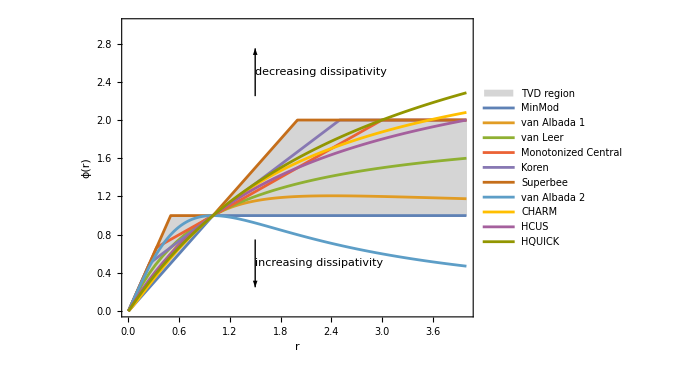

### KT Boundary conditions

```mathematica
(** Selected ghost cell reconstructions implementing certain boundary conditions **)
KT`bc`ASLE=Function[{vin},Module[{v},
	v=vin;
	v[[1]]=-v[[5]];(* Subscript[u, -2] = -Subscript[u, 2] *)
	v[[2]]=-v[[4]];(* Subscript[u, -1] = -Subscript[u, 1] *)
	v[[3]]=0*v[[3]]; (* Subscript[u, 0] = 0 *)
	v[[-2]]=2v[[-3]]-v[[-4]];(* Subscript[u, n] = 2 Subscript[u, n-1] - Subscript[u, n-2]*)
	v[[-1]]=3v[[-3]]-2v[[-4]];(* Subscript[u, n+1]= 3 Subscript[u, n-1] - 2 Subscript[u, n-2]*)
	v
]];(* Antisymmetric BC at Subscript[x, 0] and linear extrapolation at Subscript[x, n-1] *)

KT`bc`LELE=Function[{vin},Module[{v},
	v=vin;
	v[[1]]=3v[[3]]-2v[[4]];(* Subscript[u, -2] = 3 Subscript[u, 0] - 2 Subscript[u, 1]*)
	v[[2]]=2v[[3]]-v[[4]];(* Subscript[u, -1] = 2 Subscript[u, 0] - Subscript[u, 1]*)
	v[[-2]]=2v[[-3]]-v[[-4]];(* Subscript[u, n] = 2 Subscript[u, n-1] - Subscript[u, n-2]*)
	v[[-1]]=3v[[-3]]-2v[[-4]];(* Subscript[u, n+1]= 3 Subscript[u, n-1] - 2 Subscript[u, n-2]*)
	v
]];(* Linear extrapolation at Subscript[x, 0] and Subscript[x, n-1] *)

KT`bc`periodic=Function[{vin},Module[{v},
	v=vin;
	v[[1]]=v[[-5]];(* Subscript[u, -2]= Subscript[u, n-3] *)
	v[[2]]=v[[-4]];(* Subscript[u, -1]= Subscript[u, n-2] *)
	v[[-3]]=v[[3]];(* Subscript[u, n-1]= Subscript[u, 0] *)
	v[[-2]]=v[[4]];(* Subscript[u, n] = Subscript[u, 1] *)
	v[[-1]]=v[[5]];(* Subscript[u, n+1] = Subscript[u, 2] *)
	v
]];

KT`bc`antiperiodic=Function[{vin},Module[{v},
	v=vin;
	v[[1]]=-v[[-5]];(* Subscript[u, -2]= -Subscript[u, n-3] *)
	v[[2]]=-v[[-4]];(* Subscript[u, -1]= -Subscript[u, n-2] *)
	v[[-3]]=-v[[3]];(* Subscript[u, n-1]= -Subscript[u, 0] *)
	v[[-2]]=-v[[4]];(* Subscript[u, n] = -Subscript[u, 1] *)
	v[[-1]]=-v[[5]];(* Subscript[u, n+1] = -Subscript[u, 2] *)
	v
]];
```

### KT stepper

```mathematica
ClearAll[KT`stepper];
KT`stepper[ϕ_:KT`ϕ`MinMod,opts___][nx_][Δx_,x_,x12_][F_,dFdu_,Q_,BC_,pars___]:=
Compile[{{t,_Real},{v,_Real,1}},
	Module[{		
		u,(* Conserved quanties: {Subscript[u, -2],Subscript[u, -1],Subscript[u, 0],...,Subscript[u, nx-1],Subscript[u, nx],Subscript[u, nx+1]}, dim=nx+4 *)
		Δu,(* Differences of conserved quanties: {Subscript[u, -1]-Subscript[u, -2],Subscript[u, 0]-Subscript[u, -1],...,Subscript[u, nx-1]-Subscript[u, nx-2],Subscript[u, nx]-Subscript[u, nx-1],Subscript[u, nx+1]-Subscript[u, nx]}, dim=nx+3 *)
		
		ux,(* Reconstructed slopes: Subscript[(Subscript[u, x]), i]=0.5*(Subscript[u, i+1]-Subscript[u, i])*ϕ[Subscript[u, i]-Subscript[u, i-1],Subscript[u, i+1]-Subscript[u, i]^j], dim =nx+2 *)
		up12T,(* Right intermediate values at the cell interface Subscript[x, i+1/2]: Subscript[u, i+1/2]^+=Subscript[u, i+1]-Subscript[(Subscript[u, x]), i+1], dim =nx+1 *)
		um12T,(* Left intermediate values at the cell interface Subscript[x, i+1/2]: Subscript[u, i+1/2]^-=Subscript[u, i]+Subscript[(Subscript[u, x]), i], dim=nx+1 *)
		Fp12T,(* Flux through Subscript[x, i+1/2] using Subscript[u, i+1/2]^+: Subscript[F, i+1/2]^+=F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+,params], dim=nx+1 *)
		Fm12T,(* Flux through Subscript[x, i+1/2] using Subscript[u, i+1/2]^-: Subscript[F, i+1/2]^-=F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-,o,params], dim=nx+1 *)
		λp12T, (* Jacobian eigenvalues (single value) at Subscript[x, i+1/2] using Subscript[u, i+1/2]^+: Subscript[λ, i+1/2]^+=dFdu[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+,params], dim=nx+1 *)
		λm12T, (* Jacobian eigenvalues (single value) at Subscript[x, i+1/2] using Subscript[u, i+1/2]^-: Subscript[λ, i+1/2]^-=dFdu[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-,params], dim=nx+1 *)
		a12T,(* Approxmiate local speed at Subscript[x, i+1/2]: Subscript[a, i+1/2]=Max[Abs@Subscript[λ, i+1/2]^+,Abs@Subscript[λ, i+1/2]^-], dim=nx+1 *)
		H12 ,(* Numerical advection fluxes at Subscript[x, i+1/2]: Subscript[H, i+1/2]=... , dim=nx+1 *)
		
		dudx, (* Aproximate derivatives *)
		P12(* Diffusion fluxes: Subscript[P, i+1/2]=... , dim =nx+1 *)	
	},		
		(* **** Boundary condition and ODE component extraction **** *)
		u=BC[Join[{0.,0.},Take[v,{1,nx}],{0.,0.}]];
		
		(* **** PDE Convection Flux **** *)
		Δu=Differences[u];
		ux=MapThread[0.5*#2(ϕ[#1,#2])&,{Take[Δu,{1,-2}],Take[Δu,{2,-1}]}];(* [KTO2-0, eq. (2.4)*0.5*Δx]: modified to be compatible with generic\
																					flux limiters from [https://en.wikipedia.org/wiki/Flux_limiter], see also [https://en.wikipedia.org/wiki/MUSCL_scheme] *)																							
		up12T=Take[u,{3,-2}]-Take[ux,{2,-1}];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters *)
		um12T=Take[u,{2,-3}]+Take[ux,{1,-2}];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters *)

		λp12T=MapThread[dFdu[t,#1,#2,pars]&,{x12,up12T}];
		λm12T=MapThread[dFdu[t,#1,#2,pars]&,{x12,um12T}];
		a12T=MapThread[Max[Abs@#1,Abs@#2]&,{λp12T,λm12T}]; (* [KTO2-0, eq. (3.2)] [KTO2-0, footnote 2] *)
	
		Fp12T=MapThread[F[t,#1,#2,pars]&,{x12,up12T}];
		Fm12T=MapThread[F[t,#1,#2,pars]&,{x12,um12T}];
		H12=0.5*(Fp12T+Fm12T-a12T*(up12T-um12T));
		(* [KTO2-0, eq. (4.4)]:  {Subscript[H, i+1/2]}=(F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+]+F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-])/2-Subscript[a, i+1/2]/2(Subscript[u, i+1/2]^+-Subscript[u, i+1/2]^-) *)
		
		(* **** PDE Diffusion Flux **** *)
		dudx=Take[Δu,{2,-2}]/Δx;
		P12=0.5*MapThread[Q[t,#1,#3,#5,pars]+Q[t,#2,#4,#5,pars]&,{
			Join[{x12[[1]]-Δx*0.5},x],(* =Subscript[x, i+1/2]-Δx/2={Subscript[x, -1],{Subscript[x, i]}}≡{Subscript[x̂, i]}, contains cell center of second ghost cell [Subscript[x, -3/2],Subscript[x, -1/2]] *)
			Join[x,{x12[[-1]]+Δx*0.5}],(* =Subscript[x, i+1/2]+Δx/2={{Subscript[x, i]},Subscript[x, n]}≡{Subscript[x̂, i+1]}, contains cell center of penultimate ghost cell [Subscript[x, n-1/2],Subscript[x, n+1/2]] *)
			Take[u,{2,-3}], (* =Subscript[u, i] *)
			Take[u,{3,-2}],(* =Subscript[u, i+1] *)
			dudx(* =(Subscript[u, i+1]-Subscript[u, i])/Δx *)
		}];
		(* [KTO2-0, eq. (4.14)]: {Subscript[P, i+1/2]}=1/2(Q[t,Subscript[x̂, i],Subscript[u, i],(Subscript[u, i+1]-Subscript[u, i])/Δx]+Q[t,Subscript[x̂, i+1],Subscript[u, i+1],(Subscript[u, i+1]-Subscript[u, i])/Δx]) *)
				
		(* **** Result **** *)
		Return[Join[Flatten[(-Differences[H12]+Differences[P12])/Δx,1]]] (* [KTO2-0,eq.(4.13)] *)
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]
```

### KNP steppers

```mathematica
ClearAll[KNP`stepper];
KNP`stepper[ϕ_:KT`ϕ`MinMod,uxFilter_:(#&),opts___][nx_][Δx_,x_,x12_][F_,dFdu_,Q_,BC_,pars___]:=
Compile[{{t,_Real},{v,_Real,1}},
	Module[{		
		u,(* Conserved quanties: {Subscript[u, -2],Subscript[u, -1],Subscript[u, 0],...,Subscript[u, nx-1],Subscript[u, nx],Subscript[u, nx+1]}, dim=nx+4 *)
		Δu,(* Differences of conserved quanties: {Subscript[u, -1]-Subscript[u, -2],Subscript[u, 0]-Subscript[u, -1],...,Subscript[u, nx-1]-Subscript[u, nx-2],Subscript[u, nx]-Subscript[u, nx-1],Subscript[u, nx+1]-Subscript[u, nx]}, dim=nx+3 *)
		
		ux,(* Reconstructed slopes: Subscript[(Subscript[u, x]), i]=0.5*(Subscript[u, i+1]-Subscript[u, i])*ϕ[Subscript[u, i]-Subscript[u, i-1],Subscript[u, i+1]-Subscript[u, i]^j], dim =nx+2 *)
		up12T,(* Right intermediate values at the cell interface Subscript[x, i+1/2]: Subscript[u, i+1/2]^+=Subscript[u, i+1]-Subscript[(Subscript[u, x]), i+1], dim =nx+1 *)
		um12T,(* Left intermediate values at the cell interface Subscript[x, i+1/2]: Subscript[u, i+1/2]^-=Subscript[u, i]+Subscript[(Subscript[u, x]), i], dim=nx+1 *)
		Fp12T,(* Flux through Subscript[x, i+1/2] using Subscript[u, i+1/2]^+: Subscript[F, i+1/2]^+=F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+,params], dim=nx+1 *)
		Fm12T,(* Flux through Subscript[x, i+1/2] using Subscript[u, i+1/2]^-: Subscript[F, i+1/2]^-=F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-,params], dim=nx+1 *)
		λp12T, (* Jacobian eigenvalues (single value) at Subscript[x, i+1/2] using Subscript[u, i+1/2]^+: Subscript[λ, i+1/2]^+=dFdu[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+,params], dim=nx+1 *)
		λm12T, (* Jacobian eigenvalues (single value) at Subscript[x, i+1/2] using Subscript[u, i+1/2]^-: Subscript[λ, i+1/2]^-=dFdu[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-,params], dim=nx+1 *)
		ap12T,(* Approxmiate right-sided local speed at Subscript[x, i+1/2]: Subscript[a, i+1/2]^+=Max[Subscript[λ, i+1/2]^+,Subscript[λ, i+1/2]^-,0], dim=nx+1 *)
		am12T,(* Approxmiate left-sided local speed at Subscript[x, i+1/2]: Subscript[a, i+1/2]^-=Min[Subscript[λ, i+1/2]^+,Subscript[λ, i+1/2]^-,0], dim=nx+1 *)
		H12 ,(* Numerical advection fluxes at Subscript[x, i+1/2]: Subscript[H, i+1/2]=... , dim=nx+1 *)
		
		dudx, (* Aproximate derivatives *)
		P12(* Diffusion fluxes: Subscript[P, i+1/2]=... , dim =nx+1 *)	
	},		
		(* **** Boundary condition and ODE component extraction **** *)
		u=BC[Join[{0.,0.},Take[v,{1,nx}],{0.,0.}]];
		
		(* **** PDE Convection Flux **** *)
		Δu=Differences[u];
		ux=uxFilter@MapThread[0.5*#2(ϕ[#1,#2])&,{Take[Δu,{1,-2}],Take[Δu,{2,-1}]}];(* [KTO2-0, eq. (2.4)*0.5*Δx]: modified to be compatible with generic\
																					flux limiters from [https://en.wikipedia.org/wiki/Flux_limiter], see also [https://en.wikipedia.org/wiki/MUSCL_scheme] *)																							
		up12T=Take[u,{3,-2}]-Take[ux,{2,-1}];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters *)
		um12T=Take[u,{2,-3}]+Take[ux,{1,-2}];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters *)

		λp12T=MapThread[dFdu[t,#1,#2,pars]&,{x12,up12T}];
		λm12T=MapThread[dFdu[t,#1,#2,pars]&,{x12,um12T}];
		ap12T=MapThread[Max[#1,#2,0.]&,{λp12T,λm12T}]; (* [KTO2-1, eq. (3.2)] *)
		am12T=MapThread[Min[#1,#2,0.]&,{λp12T,λm12T}]; (* [KTO2-1, eq. (3.2)] *)
		
		Fp12T=MapThread[F[t,#1,#2,pars]&,{x12,up12T}];
		Fm12T=MapThread[F[t,#1,#2,pars]&,{x12,um12T}];
		H12=MapThread[{Fp,Fm,ap,am,up,um}↦If[am==0.,Fm,If[ap==0.,Fp,(ap Fm-am Fp)/(ap-am)+(ap am)/(ap-am)(up-um)]],{Fp12T,Fm12T,ap12T,am12T,up12T,um12T}];
		(* [KTO2-1, eq. (3.15)]:  {Subscript[H, i+1/2]}=(Subscript[a, i+1/2]^+F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-]-Subscript[a, i+1/2]^- F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+]+)/(Subscript[a, i+1/2]^+-Subscript[a, i+1/2]^-)+(Subscript[a, i+1/2]^+Subscript[a, i+1/2]^-)/(Subscript[a, i+1/2]^+-Subscript[a, i+1/2]^-)(Subscript[u, i+1/2]^+-Subscript[u, i+1/2]^-) *)
		
		(* **** PDE Diffusion Flux **** *)
		dudx=Take[Δu,{2,-2}]/Δx;
		P12=0.5*MapThread[Q[t,#1,#3,#5,pars]+Q[t,#2,#4,#5,pars]&,{
			Join[{x12[[1]]-Δx*0.5},x],(* =Subscript[x, i+1/2]-Δx/2={Subscript[x, -1],{Subscript[x, i]}}≡{Subscript[x̂, i]}, contains cell center of second ghost cell [Subscript[x, -3/2],Subscript[x, -1/2]] *)
			Join[x,{x12[[-1]]+Δx*0.5}],(* =Subscript[x, i+1/2]+Δx/2={{Subscript[x, i]},Subscript[x, n]}≡{Subscript[x̂, i+1]}, contains cell center of penultimate ghost cell [Subscript[x, n-1/2],Subscript[x, n+1/2]] *)
			Take[u,{2,-3}], (* =Subscript[u, i] *)
			Take[u,{3,-2}],(* =Subscript[u, i+1] *)
			dudx(* =(Subscript[u, i+1]-Subscript[u, i])/Δx *)
		}];
		(* [KTO2-0, eq. (4.14)]: {Subscript[P, i+1/2]}=1/2(Q[t,Subscript[x̂, i],Subscript[u, i],(Subscript[u, i+1]-Subscript[u, i])/Δx]+Q[t,Subscript[x̂, i+1],Subscript[u, i+1],(Subscript[u, i+1]-Subscript[u, i])/Δx]) *)
				
		(* **** Result **** *)
		Return[Join[Flatten[(-Differences[H12]+Differences[P12])/Δx,1]]] (* [KTO2-0,eq.(4.13)] *)
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]
```

```mathematica
ClearAll[KNP`stepperO1];
KNP`stepperO1[opts___][nx_][Δx_,x_,x12_][F_,dFdu_,Q_,BC_,pars___]:=
Compile[{{t,_Real},{v,_Real,1}},
	Module[{		
		u,(* Conserved quanties: {Subscript[u, -2],Subscript[u, -1],Subscript[u, 0],...,Subscript[u, nx-1],Subscript[u, nx],Subscript[u, nx+1]}, dim=nx+4 *)
		Δu,(* Differences of conserved quanties: {Subscript[u, -1]-Subscript[u, -2],Subscript[u, 0]-Subscript[u, -1],...,Subscript[u, nx-1]-Subscript[u, nx-2],Subscript[u, nx]-Subscript[u, nx-1],Subscript[u, nx+1]-Subscript[u, nx]}, dim=nx+3 *)
		
		up12T,(* Right intermediate values at the cell interface Subscript[x, i+1/2]: Subscript[u, i+1/2]^+=Subscript[u, i+1]-Subscript[(Subscript[u, x]), i+1], dim =nx+1 *)
		um12T,(* Left intermediate values at the cell interface Subscript[x, i+1/2]: Subscript[u, i+1/2]^-=Subscript[u, i]+Subscript[(Subscript[u, x]), i], dim=nx+1 *)
		Fp12T,(* Flux through Subscript[x, i+1/2] using Subscript[u, i+1/2]^+: Subscript[F, i+1/2]^+=F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+,params], dim=nx+1 *)
		Fm12T,(* Flux through Subscript[x, i+1/2] using Subscript[u, i+1/2]^-: Subscript[F, i+1/2]^-=F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-,params], dim=nx+1 *)
		λp12T, (* Jacobian eigenvalues (single value) at Subscript[x, i+1/2] using Subscript[u, i+1/2]^+: Subscript[λ, i+1/2]^+=dFdu[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+,params], dim=nx+1 *)
		λm12T, (* Jacobian eigenvalues (single value) at Subscript[x, i+1/2] using Subscript[u, i+1/2]^-: Subscript[λ, i+1/2]^-=dFdu[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-,params], dim=nx+1 *)
		ap12T,(* Approxmiate right-sided local speed at Subscript[x, i+1/2]: Subscript[a, i+1/2]^+=Max[Subscript[λ, i+1/2]^+,Subscript[λ, i+1/2]^-,0], dim=nx+1 *)
		am12T,(* Approxmiate left-sided local speed at Subscript[x, i+1/2]: Subscript[a, i+1/2]^-=Min[Subscript[λ, i+1/2]^+,Subscript[λ, i+1/2]^-,0], dim=nx+1 *)
		H12 ,(* Numerical advection fluxes at Subscript[x, i+1/2]: Subscript[H, i+1/2]=... , dim=nx+1 *)
		
		dudx, (* Aproximate derivatives *)
		P12(* Diffusion fluxes: Subscript[P, i+1/2]=... , dim =nx+1 *)	
	},		
		(* **** Boundary condition and ODE component extraction **** *)
		u=BC[Join[{0.,0.},Take[v,{1,nx}],{0.,0.}]];
		
		(* **** PDE Convection Flux **** *)
		Δu=Differences[u];
																								
		up12T=Take[u,{3,-2}];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters *)
		um12T=Take[u,{2,-3}];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters *)

		λp12T=MapThread[dFdu[t,#1,#2,pars]&,{x12,up12T}];
		λm12T=MapThread[dFdu[t,#1,#2,pars]&,{x12,um12T}];
		ap12T=MapThread[Max[#1,#2,0.]&,{λp12T,λm12T}]; (* [KTO2-1, eq. (3.2)] *)
		am12T=MapThread[Min[#1,#2,0.]&,{λp12T,λm12T}]; (* [KTO2-1, eq. (3.2)] *)
		
		Fp12T=MapThread[F[t,#1,#2,pars]&,{x12,up12T}];
		Fm12T=MapThread[F[t,#1,#2,pars]&,{x12,um12T}];
		H12=MapThread[{Fp,Fm,ap,am,up,um}↦If[am==0.,Fm,If[ap==0.,Fp,(ap Fm-am Fp)/(ap-am)+(ap am)/(ap-am)(up-um)]],{Fp12T,Fm12T,ap12T,am12T,up12T,um12T}];
		(* [KTO2-1, eq. (3.15)]:  {Subscript[H, i+1/2]}=(Subscript[a, i+1/2]^+F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-]-Subscript[a, i+1/2]^- F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+]+)/(Subscript[a, i+1/2]^+-Subscript[a, i+1/2]^-)+(Subscript[a, i+1/2]^+Subscript[a, i+1/2]^-)/(Subscript[a, i+1/2]^+-Subscript[a, i+1/2]^-)(Subscript[u, i+1/2]^+-Subscript[u, i+1/2]^-) *)
		
		(* **** Diffusion Flux **** *)
		dudx=Take[Δu,{2,-2}]/Δx;
		P12=Transpose[MapThread[Q[t,#1,#2,#3,pars]&,{
			Join[{x12[[1]]-Δx*0.5},x],(* =Subscript[x, i+1/2]-Δx/2={Subscript[x, -1],{Subscript[x, i]}}≡{Subscript[x̂, i]}, contains cell center of second ghost cell [Subscript[x, -3/2],Subscript[x, -1/2]] *)
			Take[u,{1,-2}], (* =Subscript[u, i] *)
			dudx(* =(Subscript[u, i+1]-Subscript[u, i])/Δx*)
		}]];
		(* [KTO2-0, eq. (4.14) first order reduction (Gudanov upwind)]: {Subscript[P, i+1/2]}=Q[t,Subscript[x̂, i+1],Subscript[u, i+1],(Subscript[u, i+1]-Subscript[u, i])/Δx] *)
						
		(* **** Result **** *)
		Return[Join[Flatten[(-Differences[H12]+Differences[P12])/Δx,1]]] (* [KTO2-0,eq.(4.13)] *)
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]
```

### KT solver and solution

```mathematica
ClearAll[KT`solver]
KT`solver/:Options[KT`solver]={AccuracyGoal->Automatic,PrecisionGoal->Automatic,WorkingPrecision->MachinePrecision,Method->Automatic,MaxSteps->Automatic};
KT`solver[OptionsPattern[]][stepper_:KT`stepper,ϕ_:KT`ϕ`MinMod,opts___][x0_,x1_,n_Integer,x0x1BCQ_:True][F_,dFdu_,Q_,BC_,params___][U0_][t0_,t1_,ni_:All,printQ_:True,monitorQ_:True]:=Module[{
	Δx,xi,xi12,
	v0,
	PDEcompileFkt,PDEfkt,PDEsystem,PDEv,PDEt,PDEsolver,PDEsolution,
	nt,ntSampled,tw,tm,
	sol},
	
	If[!x0x1BCQ,
		(* Subscript[x, 0] and Subscript[x, 1] are the first and last cell centers *)
		Δx=N[(x1-x0)/(n-1)];
		xi=Table[x0+Δx*i,{i,0,n-1}];
		xi12=Table[x0+Δx*(i-0.5),{i,0,n}];,
		(* Subscript[x, 0]=Subscript[x, -1/2] and Subscript[x, 1]=Subscript[x, n-1/2] are the first and last cell boundaries *)
		Δx=N[(x1-x0)/(n)];
		xi=Table[x0+Δx*(i+0.5),{i,0,n-1}];
		xi12=Table[x0+Δx*(i),{i,0,n}];
	];
	
	If[!ListQ[U0],	
		v0=Join[Differences[U0[#]&/@xi12]/Δx];,
		v0=U0;
	];
	
	PDEcompileFkt=stepper[ϕ,opts][n][Δx,xi,xi12][F,dFdu,Q,BC,params];
	PDEfkt[t_?NumericQ,v_]:=PDEcompileFkt[t,v];
	PDEsystem={Equal[PDEv[t0],v0],Equal[Derivative[1][PDEv][PDEt],PDEfkt[PDEt,PDEv[PDEt]]]};
		
	nt=0;
	tw=-AbsoluteTime[];
	PDEsolver=Inactive[NDSolveValue][PDEsystem,PDEv,{PDEt,t0,t1},
		StepMonitor:>{nt++,tm=PDEt},
		Method->OptionValue[Method],
		AccuracyGoal->OptionValue[AccuracyGoal],
		PrecisionGoal->OptionValue[PrecisionGoal],
		WorkingPrecision->OptionValue[WorkingPrecision],
		MaxSteps->OptionValue[MaxSteps]
	];
	
	If[monitorQ,
		PDEsolution=Monitor[Activate@PDEsolver,{StringForm["time step = ``",nt],StringForm["tw = ``s",ScientificForm[tw+AbsoluteTime[]]],StringForm["t = ``",NumberForm[tm,8]]}];,
		PDEsolution=Activate@PDEsolver;
	];
	tw+=AbsoluteTime[];
	tm=PDEsolution["Domain"]//Last//Last;
	
	If[printQ,Print[StringRiffle[{ToString@$KernelID," (",DateString["ISODateTime"],"): Done! ",StringForm["time steps = ``",nt], StringForm[", tw = `` s",tw]},""]]];
	sol=KT`solver`solution[<|"solution"->PDEsolution,"PDEcompileFkt"->PDEcompileFkt,"n"->n,"Δx"->Δx,"xi"->xi,"nt"->nt,"tw"->tw,"t0"->t0,"t1"->t1,"tm"->tm,"pars"->{params},"nt_sampled"->nt|>];
	
	If[IntegerQ[ni]&&ni>1,
		ntSampled=ni;
		sol=KT`solver`solution`downSample[sol,ni];		
	];
	Return[sol]	
]
```

```mathematica
ClearAll[KT`solver`solution];

(** Getter **)
KT`solver`solution[asoc_][key_]:=asoc[key] /; MemberQ[Keys[asoc], key]
KT`solver`solution[asoc_][key_Symbol]:=asoc[ToString@key] /; MemberQ[Keys[asoc], ToString@key]
KT`solver`solution[asoc_][t_]:=With[{sol=asoc["solution"],xi=asoc["xi"]},{xi,sol[t]}ᵀ/;!MissingQ[sol]]/;asoc["t0"]≤t<=asoc["t1"]||asoc["t1"]≤t<=asoc["t0"]
KT`solver`solution[asoc_][First]:=KT`solver`solution[asoc][asoc["t0"]]
KT`solver`solution[asoc_][Last]:=KT`solver`solution[asoc][asoc["t1"]]

(** StandardForm **)
MakeBoxes[KT`solver`solution[asoc_Association],StandardForm]/;BoxForm`UseIcons:=Module[{xi,n,no,Δx,nt,ntSampled},
	(* [https://mathematica.stackexchange.com/a/99914] *)
	(* [https://mathematica.stackexchange.com/a/79891] *)
	xi=With[{a=asoc["xi"]},If[MissingQ[a],{},{a[[1]],a[[2]],Skeleton[Length[a]-3],Last@a}]];
	n=With[{a=asoc["n"]},If[MissingQ[a],0,a]];
	nt=With[{a=asoc["nt"]},If[MissingQ[a],0,a]];
	ntSampled=With[{a=asoc["nt_sampled"]},If[MissingQ[a],0,a]];
	Δx=With[{a=asoc["Δx"]},If[MissingQ[a],Missing,a]];
	BoxForm`ArrangeSummaryBox[KT`solver`solution,
		KT`solver`solution[asoc],
		None,
		{{"n="<>ToString[n],"Δx="<>ToString[Δx]},{Row[{"x_i=",xi}],SpanFromLeft},{"nt="<>ToString[nt]<>" ("<>ToString[ntSampled]<>")",SpanFromLeft}},
		{},
		StandardForm,
		"Interpretable"->True
	]
]
```

```mathematica
ClearAll[KT`solver`solution`downSample]
KT`solver`solution`downSample[sol_,n_:101]:=Module[{t0,t1,int,intMethod,intOrder,asoc},
	asoc=sol[[1]];
	
	int=asoc["solution"];
	t0=asoc["t0"];
	t1=asoc["t1"];
	intMethod=int["InterpolationMethod"];
	intOrder=int["InterpolationOrder"];
	
	asoc["solution"]=Interpolation[{#,int[#]}&/@(t0+Range[0,(n-1)]/(n-1)*(t1-t0)),InterpolationOrder->intOrder,Method->intMethod];
	asoc["nt_sampled"]=n;
	
	KT`solver`solution[asoc]
]
```

```mathematica
ClearAll[KT`solver`solution`TVD]
KT`solver`solution`TVD[sol_,t_]:=(Transpose[{#[[1]][[;;-2]],Differences[#[[2]]]}&@(sol[t]ᵀ)][[All,2]]//Abs//Total)/;NumericQ[t]&&sol["t0"]≤t<=sol["t1"]

ClearAll[KT`solver`solution`Cfunction]
KT`solver`solution`Cfunction[sol_,t_/;NumericQ[t]]:=KT`solver`solution`TVD[sol,sol["t0"]]-KT`solver`solution`TVD[sol,t]
```

## FRG — Sec. IV, App. E 2, App. F

∂_t U[t,ρ]-1/2(∂_t r_b[t])(n-1)/(r_b[t]+∂_ρ U[t,ρ])-1/2(∂_t r_b[t])1/(r_b[t]+∂_ρ U[t,ρ]+2ρ∂_ρ^2 U[t,ρ])=0,
∂_t U[t,σ]-1/2(∂_t r_b[t])(n-1)/(r_b[t]+∂_σ U[t,σ]/σ)-1/2(∂_t r_b[t])1/(r_b[t]+∂_σ^2 U[t,σ])=0

∂_t u[t,σ]-∂_σ (1/2(∂_t r_b[t])(n-1)/(r_b[t]+u[t,σ]/σ))-∂_σ (1/2(∂_t r_b[t])1/(r_b[t]+∂_σ u[t,σ]))=0,
∂_t u[t,σ]+∂_σ F[t,σ,u]=∂_σ Q[t,σ,u,∂_σ u],
F[t,σ,u]=-1/2(∂_t r_b[t])(n-1)/(r_b[t]+u[t,σ]/σ)=1/2(n-1)r_b[t]/(r_b[t]+u[t,σ]/σ),
(∂F[t,σ,u])/(∂u)=+1/2(∂_t r_b[t])((n-1)σ)/(r_b[t]σ+u[t,σ])^2=-1/2(n-1)(r_b[t]σ)/(r_b[t]σ+u[t,σ])^2,
Q[t,σ,u,∂_σ u]=Q[t,∂_σ u]=1/2(∂_t r_b[t])1/(r_b[t]+∂_σ u[t,σ])=-1/2 r_b[t]/(r_b[t]+∂_σ u[t,σ]),
where r_b[t]=Λ Exp[-t] and  ∂_t r_b[t]=-Λ Exp[-t]=-r_b[t].

l=3;
FoldList[D,U[σ^2/2]==U[σ],ConstantArray[σ,l]];
Solve[%,Table[Derivative[n][U][σ^2/2],{n,0,l}]]//First//Expand;
%/.Derivative[n_][U][1/2σ^2]:>Derivative[n][U][ρ]/.U[1/2σ^2]->U[ρ]
Solve[%%%,Table[Derivative[n][U][σ],{n,0,l}]]//First//Expand;
%/.σ→√(2ρ)/.U[√(2ρ)]->U[σ]/.Derivative[n_][U][√(2ρ)]:>Derivative[n][U][σ]

∂_t U[t,ρ]-1/2(∂_t r_b[t])(n-1)/(r_b[t]+∂_ρ U[t,ρ])-1/2(∂_t r_b[t])1/(r_b[t]+∂_ρ U[t,ρ]+2ρ∂_ρ^2 U[t,ρ])=0,
∂_t V[t,z]-1/2(∂_t r_b[t])(n-1)/n 1/(r_b[t]+∂_z V[t,z])-1/2(∂_t r_b[t])1/n 1/(r_b[t]+∂_z V[t,z]+2z∂_z^2 V[t,z])=0, with {U[t,ρ]→n V[t,z],U^(m,n)[t,ρ]→n^(1-m)V[t,z],ρ→nz};
∂_t V[t,z]-1/2(∂_t r_b[t])1/(r_b[t]+∂_z V[t,z])-O[1/n]^1=0
(ⅇ^-t Λ)/(2 (ⅇ^-t Λ+v^(0,1)[t,z]))+v^(1,0)[t,z]=0, where r_b[t]=Λ Exp[-t] and  ∂_t r_b[t]=-Λ Exp[-t]=-r_b[t];
v^(1,0)[t,z]-(ⅇ^-t Λ)/(2 (ⅇ^-t Λ+v[t,z])^2)v^(0,1)[t,z]=0, where v[t,z]=∂_z V[t,z]

### Method of characteristics and shock position — Sub.Sub.Sec. IV E 1

Derivative[1,0][U][t,y]-1/2 drbdt(n)/(rb+D[U[t,x],x]/x)-1/2 drbdt 1/(rb+D[U[t,x],x,x])/.{D[U[t,x],x]->D[U[t,y],y]x,D[U[t,x],x,x]->D[U[t,y],y]+2y D[U[t,y],y,y]}
%/(n)/.{Derivative[m_,n_][U][t,y]:>(n)^(1-n)Derivative[m,n][V][t,z],y→(n)z}//Simplify
Series[%,{nπ,∞,0}]/.{rb->Λ Exp[-t] ,drbdt→-Λ Exp[-t]}//Normal

D[%,z]/.({#,D[#,z],D[#,t]}&@(D[V[t,z],z]→v[t,z]))

{v^(1,0)[t,z]-(ⅇ^-t Λ)/(2 (ⅇ^-t Λ+v[t,z])^2)v^(0,1)[t,z]=0 , v[0,z]==v_0[r]}
⇔ a[t,z,v]v^(1,0)[t,z]+b[t,z,v]v^(0,1)[t,z]==c[t,z,v], with a[t,z,v]=1,b[t,z,v]=-(ⅇ^-t Λ)/(2 (ⅇ^-t Λ+v)^2) and  c[t,z,v]=0 ;
Lagrange–Charpit equations [https://en.wikipedia.org/wiki/Method_of_characteristics];
{
D[t[s],s]==a[t,z,v]==1,
D[z[s],s]==b[t,z,v]==-(ⅇ^-t Λ)/(2 (ⅇ^-t Λ+v)^2),
D[v[s],s]==c[t,z,v]==0,
t[s=0]==0,
z[s=0]==z_0,
v[s=0]==v_0[z_0]
}

t[s]=s=t;
v[t]=v0[z0];
 z[t]==z0-∫_0^t ds(ⅇ^-s Λ)/(2 (ⅇ^-s Λ+v0[z0])^2)=z0-((-1+ⅇ^t) Λ)/(2 (Λ+v0[z0]) (Λ+ⅇ^t v0[z0])) ⟺ dz/ds=-(ⅇ^-s Λ)/(2 (ⅇ^-s Λ+v0[z0])^2),

-(ⅇ^-t Λ)/(2 (ⅇ^-t Λ+v)^2)/.t→s/.v→v0
y0+Integrate[%,{s,0,t}]

%-(y0-1/(2(Λ Exp[-t]+v0))+1/(2(Λ+v0)))//Simplify

```mathematica
ON∞d0`ρ[v0_,Λ_:1][t_,z0_]:=z0-((-1+ⅇ^t) Λ)/(2 (Λ+v0[z0]) (Λ+ⅇ^t v0[z0])) 
ON∞d0`ρ[v0_,Λ_:1][∞,z0_]:=z0-Λ/(2 v0[z0] (Λ+v0[z0]))
```

```mathematica
ON∞d0`ρ0min[v0_,Λ_:1][t_]:=Module[{r},Max[If[Abs[Im[#]]>0||!NumberQ[#],0,#]&/@Flatten[{0,r+$MachineEpsilon/.NSolve[Λ+ⅇ^t v0[r]==0,r]}]]]
ON∞d0`ρ0min[v0_,Λ_:1][∞]:=0
ON∞d0`ut[v0_,Λ_:1,ρ_:ON∞d0`ρ][t_,r_]:=v0[Module[{x},x/.FindRoot[ρ[v0,Λ][t,x]-r,{x,1,ON∞d0`ρ0min[v0,Λ][t]}]]]
```

```mathematica
ξB={2+(Log[(a-ⅇ^-t Λ)/(a-Λ)]-Log[(1+ⅇ^-t Λ)/(1+Λ)])/(2 (1+a)),8+((-1+ⅇ^t) Λ)/(2 (a ⅇ^t-Λ) (-a+Λ)),8-((-1+ⅇ^t) Λ)/(2 (1+Λ) (ⅇ^t+Λ))};
```

```mathematica
ξx[a_,Λ_][t_]:=With[{ρ=2+(Log[(a-ⅇ^-t Λ)/(a-Λ)]-Log[(1+ⅇ^-t Λ)/(1+Λ)])/(2 (1+a)),ρL=8+((-1+ⅇ^t) Λ)/(2 (a ⅇ^t-Λ) (-a+Λ)),ρR=8-((-1+ⅇ^t) Λ)/(2 (1+Λ) (ⅇ^t+Λ))},{
If[Re@ρ<Re@ρL&&Re@ρ>=0&&Re@ρL>=0&&Im[ρ]<$MachineEpsilon,{{√(2ρL),-a √(2ρL)},{√(2ρR),√(2ρR)}},{{√(2ρR),√(2ρR)}}],
If[Re@ρ<Re@ρL&&Re@ρ>=0&&Im[ρ]<$MachineEpsilon,{{√(2ρ),√(2ρ)},{√(2ρ),-a √(2ρ)}},Nothing]
}]
```

```mathematica
ξy[a_,Λ_][t_]:=With[{ρ=2+(Log[(a-ⅇ^-t Λ)/(a-Λ)]-Log[(1+ⅇ^-t Λ)/(1+Λ)])/(2 (1+a)),ρL=8+((-1+ⅇ^t) Λ)/(2 (a ⅇ^t-Λ) (-a+Λ)),ρR=8-((-1+ⅇ^t) Λ)/(2 (1+Λ) (ⅇ^t+Λ))},{
If[Re@ρ<Re@ρL&&Re@ρ>=0&&Re@ρL>=0&&Im[ρ]<$MachineEpsilon,{{ρL,-a},{ρR,1}},{{ρR,1}}],
If[Re@ρ<Re@ρL&&Re@ρ>=0&&Im[ρ]<$MachineEpsilon,{{ρ,1},{ρ,-a}},Nothing]
}]
```

```mathematica
tc0=t/.FindRoot[8+((-1+ⅇ^t) Λ)/(2 (a ⅇ^t-Λ) (-a+Λ))==2+(Log[(a-ⅇ^-t Λ)/(a-Λ)]-Log[(1+ⅇ^-t Λ)/(1+Λ)])/(2 (1+a))/.a->0ac/.Λ->10^10,{t,25}]
tc1=t/.FindRoot[8+((-1+ⅇ^t) Λ)/(2 (a ⅇ^t-Λ) (-a+Λ))==2+(Log[(a-ⅇ^-t Λ)/(a-Λ)]-Log[(1+ⅇ^-t Λ)/(1+Λ)])/(2 (1+a))/.a->1ac/.Λ->10^10,{t,25}]
tc2=t/.FindRoot[8+((-1+ⅇ^t) Λ)/(2 (a ⅇ^t-Λ) (-a+Λ))==2+(Log[(a-ⅇ^-t Λ)/(a-Λ)]-Log[(1+ⅇ^-t Λ)/(1+Λ)])/(2 (1+a))/.a->2ac/.Λ->10^10,{t,25}]
```

25.7176

25.4691

25.2702

```mathematica
ξx[0,10^10][tc0-10^-14]
ξx[ac,10^10][tc1-10^-14]
ξx[2ac,10^10][tc2-10^-14]
```

{{{1.11476,0.},{3.88117,3.88117}},{{1.11476,1.11476},{1.11476,0.}}}

{{{1.13092,-0.021432},{3.88329,3.88329}},{{1.13092,1.13092},{1.13092,-0.021432}}}

{{{1.14637,-0.0434497},{3.88534,3.88534}},{{1.14637,1.14637},{1.14637,-0.0434497}}}

Figure: f[x]=V[x]-1/2 Log[x] — Fig. 2 (fofy.pdf)

```mathematica
figFofy`xtick={0,1/2,2,4,6,8,10};
figFofy`xlabel={0,MaTeX["\\tfrac{1}{2}",FontSize -> 10],2,4,6,8,10};
figFofy`ytick={0.5,1/2. + Log[2]/2,1,1.5,2};
figFofy`ylabel={0.5,MaTeX["f(\\tfrac{1}{2})",FontSize -> 10],1,1.5,2};

Vofy-1/2 Log[y]
{%/.a->0,%/.a->1/12 (3-Log[16]),%/.a->1/12 (3-Log[16])*2};
Plot[%,{y,0,10},
	PlotRange->{{0,10},{0.5,2}},
	PlotStyle->{{emorot, AbsoluteThickness[thickness]},{gruen, AbsoluteThickness[thickness]},{goetheblau, AbsoluteThickness[thickness]}},
	PlotLegends ->
	Placed[
		LineLegend[
			Directive[#, AbsoluteThickness[thickness]]&/@{emorot,gruen,goetheblau},
			MaTeX[#, FontSize -> fontsize]&/@{"a=0","a=a_\\mathrm{c}","a=2a_\\mathrm{c}"},
			Spacings->0.5,
			LegendLayout -> "Row",
			LegendMarkerSize -> {15,10},
			Alignment -> { Left, Center }
		],
		{ Right, 0.09 }
	],
	Frame->True,FrameTicks->{{Transpose@{figFofy`ytick,figFofy`ylabel},Transpose@{figFofy`ytick,ConstantArray["",Length@figFofy`ytick]}},{Transpose@{figFofy`xtick,figFofy`xlabel},Transpose@{figFofy`xtick,ConstantArray["",Length@figFofy`xtick]}}},
	FrameStyle -> BlackFrame,
	GridLines -> {figFofy`xtick[[2;;-2]],figFofy`ytick[[2;;-2]]},
	GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]]
]
```

Figure: Characteristic curves and ξ[t] as well as ξ_4^±[t] for a=0 — Fig. 4 (characteristics.pdf)

```mathematica
ClearAll[figCharacteristics`cfunc,figCharacteristics`genLine]
figCharacteristics`cfunc=Blend[ { goetheblau,sonnengelb}, (#/4.5)^0.33] &;
figCharacteristics`genLine[char_,cfunc_,n_:200]:=Module[{dat,tmax,trange},
	tmax=Solve[char[[1]]==0,t,Reals];
	If[tmax=!={},tmax=t/.First[tmax]//N,tmax=60.];
	trange=Range[0,n]/n*tmax;
	dat=Table[char,{t,trange}]//Re;
	{Blend[{cfunc[#[[1,3]]],cfunc[#[[2,3]]]},0.5],Line[#[[All,{1,2}]]]}&/@Transpose[{dat[[;;-2]],dat[[2;;]]}]
]
```

```mathematica
Λ=10^10;a=0;
DeleteCases[Table[1/2 x0^2,{x0,1/4,4+1/2,1/4}]~Join~{8-1/1000,8+1/1000},8];
y↦Evaluate[dVdy];
figCharacteristics`dat=Table[With[{y=ON∞d0`ρ[%,Λ][t,z0]},{√(2y),t,With[{x=√(2z0)},Piecewise[{{√(2y), -2≤x≤2||x>4||x<-4}, {0, True}}]],√(2z0)}],{z0,%%}]//Quiet;
figCharacteristics`lines=Graphics[figCharacteristics`genLine[#,figCharacteristics`cfunc]]&/@figCharacteristics`dat;

ParametricPlot[{{√(2ξB[[1]]),t},{√(2ξB[[2]]),t},{√(2ξB[[3]]),t},{t,tc0}},{t,0,60},
PlotStyle->{
		{Black,AbsoluteThickness[thickness]},
		{Black,AbsoluteThickness[thickness],AbsoluteDashing[{dashing,dashing}]},
		{Black,AbsoluteThickness[thickness],AbsoluteDashing[{0.25*dashing,dashing}]},
		{emorot,AbsoluteThickness[thickness],AbsoluteDashing[dashing]}
	},
PlotLegends ->
	Placed[
		LineLegend[
			Automatic,
			MaTeX[#, FontSize -> fontsize]&/@{"\\xi_\\mathrm{s}(t)","\\xi_\\mathrm{r}^-(t)","\\xi_\\mathrm{r}^+(t)","t=25.718"},
			Spacings->0.5,
			LegendLayout -> "Column",
			LegendMarkerSize -> {20,10},
			Alignment -> { Left, Center }
		],
		{ 0.66, 0.80}
	]];
Show[{
	ListPlot[
		{{}},
		AspectRatio->1,
		PlotRange->{{0,4.5},{0,60}},
		Frame->True,
		FrameLabel->{MaTeX["x",FontSize->fontsize],MaTeX["t",FontSize->fontsize]},
		(*GridLines -> {{1,2,3,4},{10,20,tc0,30,40,50}},*)
		GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]]
	],
	figCharacteristics`lines,
	%
}]

FindRoot[ξB[[1]]==ξB[[2]],{t,15}]

ClearAll[a,Λ]
```

### KT infinite-N limit — Sub.Sub.Sec. IV E 2 and App. F 1

```mathematica
ON0dLargeNLimit`PDE`F={t,x,u,pars}↦With[{rb=pars[[1]]Exp[-t]},0.5((rb x)/(rb x+u))];
ON0dLargeNLimit`PDE`dFdu={t,x,u,pars}↦With[{rb=pars[[1]]Exp[-t]},-0.5((rb x)/(rb x+u)^2)];
ON0dLargeNLimit`PDE:=Sequence[ON0dLargeNLimit`PDE`F,ON0dLargeNLimit`PDE`dFdu,0&,KT`bc`ASLE];
```

```mathematica
ON0dLargeNLimit`RP0acsol=Import["trajectories/LargeNLimit_0ac_1E10_1500.mx.gz"];
ON0dLargeNLimit`RP1acsol=Import["trajectories/LargeNLimit_1ac_1E10_1500.mx.gz"];
ON0dLargeNLimit`RP2acsol=Import["trajectories/LargeNLimit_2ac_1E10_1500.mx.gz"];

#->ToExpression[#][tw]&/@{"ON0dLargeNLimit`RP0acsol","ON0dLargeNLimit`RP1acsol","ON0dLargeNLimit`RP2acsol"};
twFRG=DeleteDuplicates[twFRG~Join~Association[%]];
```

Single computations

x0=0.;x1=5;Λin=10^10;ain=0ac;
x↦Evaluate[Vofx/.a→ain];
KT`solver[AccuracyGoal→10,PrecisionGoal→10][KT`stepper,KT`ϕ`MinMod][x0,x1,1500,False][ON0dLargeNLimit`PDE,{Λin}][%][0,60,6001];
ON0dLargeNLimit`RP0acsol=KT`solver`solution[%[[1]]~Join~<|a→ain,Λ→Λin|>]
ClearAll[x0,x1,nx,a,Λ]

Export["trajectories/LargeNLimit_0ac_1E10_1500.mx.gz",ON0dLargeNLimit`RP0acsol]
ClearAll[ON0dLargeNLimit`RP0acsol]

x0=0.;x1=5;Λin=10^10;ain=ac;
x↦Evaluate[Vofx/.a→ain];
KT`solver[AccuracyGoal→10,PrecisionGoal→10][KT`stepper,KT`ϕ`MinMod][x0,x1,1500,False][ON0dLargeNLimit`PDE,{Λin}][%][0,60,6001];
ON0dLargeNLimit`RP1acsol=KT`solver`solution[%[[1]]~Join~<|a→ain,Λ→Λin|>]
ClearAll[x0,x1,nx,a,Λ]

Export["trajectories/LargeNLimit_1ac_1E10_1500.mx.gz",ON0dLargeNLimit`RP1acsol]
ClearAll[ON0dLargeNLimit`RP1acsol]

x0=0.;x1=5;Λin=10^10;ain=2ac;
x↦Evaluate[Vofx/.a→ain];
KT`solver[AccuracyGoal→10,PrecisionGoal→10][KT`stepper,KT`ϕ`MinMod][x0,x1,1500,False][ON0dLargeNLimit`PDE,{Λin}][%][0,60,6001];
ON0dLargeNLimit`RP2acsol=KT`solver`solution[%[[1]]~Join~<|a→ain,Λ→Λin|>]
ClearAll[x0,x1,nx,a,Λ]

Export["trajectories/LargeNLimit_2ac_1E10_1500.mx.gz",ON0dLargeNLimit`RP2acsol]
ClearAll[ON0dLargeNLimit`RP2acsol]

(* n_min for double prec with a=0 and a=a_c *)
x0=0.;x1=5;Λin=10^10;ain=0ac;
x↦Evaluate[Vofx/.a→ain];
sol=KT`solver[AccuracyGoal→10,PrecisionGoal→10][KT`stepper,KT`ϕ`MinMod][x0,x1,120,False][ON0dLargeNLimit`PDE,{Λin}][%][0,60,61];
ClearAll[x0,x1,nx,a,Λ]
sol[60][[2,2]]/sol[Δx]-1//Abs

x0=0.;x1=5;Λin=10^10;ain=1*ac;
x↦Evaluate[Vofx/.a→ain];
sol=KT`solver[AccuracyGoal→10,PrecisionGoal→10][KT`stepper,KT`ϕ`MinMod][x0,x1,280,False][ON0dLargeNLimit`PDE,{Λin}][%][0,60,61];
ClearAll[x0,x1,nx,a,Λ]
sol[60][[2,2]]/sol[Δx]-1//Abs

#### Figure: 2D Plots of N→∞ flows for a=0, a=a_c, a=2 a_c — Fig. 5 (largeN _flows.pdf)

```mathematica
figLargeNflows`cfunc=Blend[{goetheblau,emorot},(#/60)^0.5]&;
```

```mathematica
ain=0;ti={0,24,25.7,26.6,60};
figLargeNflows`p1`metadata={
	Text[MaTeX["v(t,x)", FontSize -> fontsize], { 0.5, 2.5 }],
	Text[MaTeX["a=0", FontSize -> fontsize], { 4.5, 2.5 }],
	Text[MaTeX["N\\rightarrow\\infty", FontSize -> fontsize], { 4.5, 1.5 }],
	Text[MaTeX[StringForm["n = `` \\mkern30mu x_\\mathrm{max} = `` \\mkern30mu  \\Lambda = 10^{``} \\mkern30mu  r_\\mathrm{IR} \\approx 10^{``}",1500,5,10,-18], FontSize -> fontsize],{2.5,-0.5}]
};
figLargeNflows`p1=Show[{
	ListLinePlot[ON0dLargeNLimit`RP0acsol[ti[[1]]],PlotStyle->figLargeNflows`cfunc[ti[[1]]],PlotRange->{{0,5},{-0.9,5}},Frame->True,
		GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]],Epilog->figLargeNflows`p1`metadata,
		PlotLegends ->
	Placed[
		LineLegend[
			Table[Directive[figLargeNflows`cfunc[t], AbsoluteThickness[thickness]],{t,ti}],
			Table[MaTeX[StringForm["t=``",t], FontSize -> fontsize],{t,ti}],
			Spacings->0.25,
			LegendLayout -> "Row",
			LegendMarkerSize -> {10,10},
			Alignment -> { Left, Center }
		],
		{ Left, Top }
	]
		],
	ListPlot[ξx[ain,10^10][ti[[1]]],PlotRange->All,PlotMarkers->{PolMarker["Disk"],PolMarker["Square"]},PlotStyle->{figLargeNflows`cfunc[ti[[1]]]}],
	Table[Show[{ListLinePlot[ON0dLargeNLimit`RP0acsol[t],PlotStyle->figLargeNflows`cfunc[t]],ListPlot[ξx[ain,10^10][t],PlotRange->All,PlotMarkers->{PolMarker["Disk"],PolMarker["Square"]},PlotStyle->{figLargeNflows`cfunc[t]}]}],{t,ti[[2;;]]}]
}]
figLargeNflows`p1`data=Table[{ON0dLargeNLimit`RP0acsol[t],ξx[ain,10^10][t]},{t,ti}];
ClearAll[ain,ti]
```

```mathematica
ain=ac;ti={0,24,25.45,26.5,60};
figLargeNflows`p2`metadata={
	Text[MaTeX["v(t,x)", FontSize -> fontsize], { 0.5, 2.5 }],
	Text[MaTeX["a=a_\\mathrm{c}", FontSize -> fontsize], { 4.5, 2.5 }],
	Text[MaTeX["N\\rightarrow\\infty", FontSize -> fontsize], { 4.5, 1.5 }],
	Text[MaTeX[StringForm["n = `` \\mkern30mu x_\\mathrm{max} = `` \\mkern30mu  \\Lambda = 10^{``} \\mkern30mu  r_\\mathrm{IR} \\approx 10^{``}",1500,5,10,-18], FontSize -> fontsize],{2.5,-0.5}]
};
figLargeNflows`p2=Show[{
	ListLinePlot[ON0dLargeNLimit`RP1acsol[ti[[1]]],PlotStyle->figLargeNflows`cfunc[ti[[1]]],PlotRange->{{0,5},{-0.9,5}},Frame->True,
		GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]],Epilog->figLargeNflows`p2`metadata,
		PlotLegends ->
	Placed[
		LineLegend[
			Table[Directive[figLargeNflows`cfunc[t], AbsoluteThickness[thickness]],{t,ti}],
			Table[MaTeX[StringForm["t=``",t], FontSize -> fontsize],{t,ti}],
			Spacings->0.25,
			LegendLayout -> "Row",
			LegendMarkerSize -> {10,10},
			Alignment -> { Left, Center }
		],
		{ Left, Top }
	]
		],
	ListPlot[ξx[ain,10^10][ti[[1]]],PlotRange->All,PlotMarkers->{PolMarker["Disk"],PolMarker["Square"]},PlotStyle->{figLargeNflows`cfunc[ti[[1]]]}],
	Table[Show[{ListLinePlot[ON0dLargeNLimit`RP1acsol[t],PlotStyle->figLargeNflows`cfunc[t]],ListPlot[ξx[ain,10^10][t],PlotRange->All,PlotMarkers->{PolMarker["Disk"],PolMarker["Square"]},PlotStyle->{figLargeNflows`cfunc[t]}]}],{t,ti[[2;;]]}]
}]
figLargeNflows`p2`data=Table[{ON0dLargeNLimit`RP1acsol[t],ξx[ain,10^10][t]},{t,ti}];
ClearAll[ain,ti]
```

```mathematica
ain=2ac;ti={0,24,25.25,26,60};
figLargeNflows`p3`metadata={
	Text[MaTeX["v(t,x)", FontSize -> fontsize], { 0.5, 2.5 }],
	Text[MaTeX["a=2a_\\mathrm{c}", FontSize -> fontsize], { 4.5, 2.5 }],
	Text[MaTeX["N\\rightarrow\\infty", FontSize -> fontsize], { 4.5, 1.5 }],
	Text[MaTeX[StringForm["n = `` \\mkern30mu x_\\mathrm{max} = `` \\mkern30mu  \\Lambda = 10^{``} \\mkern30mu  r_\\mathrm{IR} \\approx 10^{``}",1500,5,10,-18], FontSize -> fontsize],{2.5,-0.5}]
};
figLargeNflows`p3=Show[{
	ListLinePlot[ON0dLargeNLimit`RP2acsol[ti[[1]]],PlotStyle->figLargeNflows`cfunc[ti[[1]]],PlotRange->{{0,5},{-0.9,5}},Frame->True,
		GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]],Epilog->figLargeNflows`p3`metadata,
		PlotLegends ->
	Placed[
		LineLegend[
			Table[Directive[figLargeNflows`cfunc[t], AbsoluteThickness[thickness]],{t,ti}],
			Table[MaTeX[StringForm["t=``",t], FontSize -> fontsize],{t,ti}],
			Spacings->0.25,
			LegendLayout -> "Row",
			LegendMarkerSize -> {10,10},
			Alignment -> { Left, Center }
		],
		{ Left, Top }
	]
		],
	ListPlot[ξx[ain,10^10][ti[[1]]],PlotRange->All,PlotMarkers->{PolMarker["Disk"],PolMarker["Square"]},PlotStyle->{figLargeNflows`cfunc[ti[[1]]]}],
	Table[Show[{ListLinePlot[ON0dLargeNLimit`RP2acsol[t],PlotStyle->figLargeNflows`cfunc[t]],ListPlot[ξx[ain,10^10][t],PlotRange->All,PlotMarkers->{PolMarker["Disk"],PolMarker["Square"]},PlotStyle->{figLargeNflows`cfunc[t]}]}],{t,ti[[2;;]]}]
}]
figLargeNflows`p3`data=Table[{ON0dLargeNLimit`RP2acsol[t],ξx[ain,10^10][t]},{t,ti}];
ClearAll[ain,ti]
```

```mathematica
figLargeNflows=ResourceFunction["PlotGrid"][
	{
		{figLargeNflows`p1},
		{figLargeNflows`p2},
	    {figLargeNflows`p3}
	},
	ImageSize -> { column`width, All },
	FrameLabel -> { MaTeX["x", FontSize -> fontsize] }
]
figLargeNflows`data={figLargeNflows`p1`data,figLargeNflows`p2`data,figLargeNflows`p3`data}//N;
Export["data/largeN_flows.json",%]
```

```mathematica
ResourceFunction["PlotGrid"][
	{
		{figLargeNflows`p1},
	    {figLargeNflows`p3}
	},
	ImageSize -> { column`width, All },
	FrameLabel -> { MaTeX["x", FontSize -> fontsize] }
]
```

Figure: 3D Plot of Flows a=0 — Fig. 6  (largeN_0_flow3D.pdf)

```mathematica
figLargeN0flow3D`cfunc=Blend[{goetheblau,emorot},(#2/60)^0.5]&;
figLargeN0flow3D`ti={Table[t,{t,0,20,1}],Table[t,{t,20,30,1/10}],Table[t,{t,30,60,1}]}//Flatten//DeleteDuplicates//Sort//N
figLargeN0flow3D`data=Table[{#[[1]],t,#[[2]]}&/@ON0dLargeNLimit`RP0acsol[t][[;;;;2]],{t,figLargeN0flow3D`ti}]//Flatten[#,1]&;
```

```mathematica
figLargeN0flow3D`view={-0.91,2.48,2.09}
figLargeN0flow3D=ListPlot3D[
	figLargeN0flow3D`data,
	
	PlotRange -> { { 0.0, 5 }, { 0, 60 }, { -.9, 5.5 } },
	
	AxesLabel -> { MaTeX["x", FontSize -> fontsize], MaTeX["t", FontSize -> fontsize] , MaTeX["v ( t, x )", FontSize -> fontsize] },
	
	ColorFunction -> figLargeN0flow3D`cfunc,ColorFunctionScaling->False, ViewPoint->Dynamic[figLargeN0flow3D`view],
	BaseStyle -> { FontFamily -> fontfamily, FontSize -> 10 },
	TicksStyle->Directive[Black],
	PlotRangePadding -> None,
	Boxed -> True,
	BoxStyle -> BlackFrame,
	Ticks->{{0,1,2,3,4,5},{0,20,40,60},{0,2,4}},
	ImageSize -> { column`width, All }
]
Dynamic[figLargeN0flow3D`view]
```

```mathematica
figLargeN0flow3D`ξx[a_,Λ_][t_]:=With[{ρ=2+(Log[(a-ⅇ^-t Λ)/(a-Λ)]-Log[(1+ⅇ^-t Λ)/(1+Λ)])/(2 (1+a))},{{√(2ρ),t,√(2ρ)+0.05},{√(2ρ)+0.025,t,-a √(2ρ)+0.025}}]
figLargeN0flow3D`ξx4p[a_,Λ_][t_]:=With[{ρR=8-((-1+ⅇ^t) Λ)/(2 (1+Λ) (ⅇ^t+Λ))},{√(2ρR),t,√(2ρR)}]
figLargeN0flow3D`ξx4m[a_,Λ_][t_]:=With[{ρL=8+((-1+ⅇ^t) Λ)/(2 (a ⅇ^t-Λ) (-a+Λ))},{√(2ρL)-0.05,t,-a √(2ρL)+0.05}]
Show[{figLargeN0flow3D,ParametricPlot3D[figLargeN0flow3D`ξx4p[0ac,10^10][t],{t,0,60},PlotStyle->{sonnengelb,AbsoluteThickness[thickness]}],ParametricPlot3D[figLargeN0flow3D`ξx4m[0ac,10^10][t],{t,0,25.7},PlotStyle->{sonnengelb,AbsoluteThickness[thickness]}],ParametricPlot3D[figLargeN0flow3D`ξx[0ac,10^10][t],{t,0,25.7},PlotStyle->{hellesgruen,AbsoluteThickness[thickness]}]}]
```

```mathematica
{figLargeN0flow3D`data,Table[Flatten[{{figLargeN0flow3D`ξx4p[0,10^10][t]},{figLargeN0flow3D`ξx4m[0,10^10][t]},figLargeN0flow3D`ξx[0,10^10][t]},1]/.t->25.7*i,{i,0,1,1/100}]};
Export["data/largeN_0_flow3D.json",%]
```

#### Figure: 3D Plot of Flows a=0 —(largeN_0_flow3D-noBox.pdf), PhD Thesis M. J. Steil title picture

```mathematica
figLargeN0flow3D`cfunc=Blend[{goetheblau,emorot},(#2/60)^0.5]&;
figLargeN0flow3D`ti={Table[t,{t,0,20,1}],Table[t,{t,20,30,1/20}],Table[t,{t,30,60,1}]}//Flatten//DeleteDuplicates//Sort//N;
figLargeN0flow3D`data=Table[{#[[1]],t,#[[2]]}&/@ON0dLargeNLimit`RP0acsol[t][[;;;;2]],{t,figLargeN0flow3D`ti}]//Flatten[#,1]&;
```

```mathematica
figLargeN0flow3D`view={-0.91,2.48,2.09}
figLargeN0flow3D=ListPlot3D[
	figLargeN0flow3D`data,
	
	PlotRange -> { { 0.0, 5 }, { 0, 60 }, { -.9, 5.5 } },
	
		
	ColorFunction -> figLargeN0flow3D`cfunc,ColorFunctionScaling->False, ViewPoint->Dynamic[figLargeN0flow3D`view],
	PlotRangePadding -> None,
	Boxed -> False,
	ImageSize -> { column`width, All }
];
```

{-0.91,2.48,2.09}

```mathematica
figLargeN0flow3D`ξx[a_,Λ_][t_]:=With[{ρ=2+(Log[(a-ⅇ^-t Λ)/(a-Λ)]-Log[(1+ⅇ^-t Λ)/(1+Λ)])/(2 (1+a))},{{√(2ρ),t,√(2ρ)+0*0.05},{√(2ρ)+0.025,t,-a √(2ρ)+0*0.025}}]
figLargeN0flow3D`ξx4p[a_,Λ_][t_]:=With[{ρR=8-((-1+ⅇ^t) Λ)/(2 (1+Λ) (ⅇ^t+Λ))},{√(2ρR),t,√(2ρR)}]
figLargeN0flow3D`ξx4m[a_,Λ_][t_]:=With[{ρL=8+((-1+ⅇ^t) Λ)/(2 (a ⅇ^t-Λ) (-a+Λ))},{√(2ρL)-0.01,t,-a √(2ρL)+0.01}]
Show[{Show[figLargeN0flow3D,Axes->False,ImageSize->400],ParametricPlot3D[figLargeN0flow3D`ξx4p[0ac,10^10][t],{t,0,60},PlotStyle->{sonnengelb,AbsoluteThickness[thickness]}],ParametricPlot3D[figLargeN0flow3D`ξx4m[0ac,10^10][t],{t,0,25.7},PlotStyle->{sonnengelb,AbsoluteThickness[thickness]}],ParametricPlot3D[figLargeN0flow3D`ξx[0ac,10^10][t],{t,0,25.7},PlotStyle->{hellesgruen,AbsoluteThickness[thickness]}]}]
```

Figure: 3D Plot of Flows a=2 a_c — Fig. 7  (largeN_2_flow3D.pdf)

```mathematica
figLargeN2flow3D`cfunc=Blend[{goetheblau,emorot},(#2/60)^0.5]&;
figLargeN2flow3D`ti={Table[t,{t,0,20,1}],Table[t,{t,20,30,1/10}],Table[t,{t,30,60,1}]}//Flatten//DeleteDuplicates//Sort//N;
figLargeN2flow3D`data=Table[{#[[1]],t,#[[2]]}&/@ON0dLargeNLimit`RP2acsol[t][[;;;;2]],{t,figLargeN2flow3D`ti}]//Flatten[#,1]&;
```

```mathematica
figLargeN2flow3D`view={-0.91,2.48,2.09}
figLargeN2flow3D=ListPlot3D[
	figLargeN2flow3D`data,
	
	PlotRange -> { { 0.0, 5 }, { 0, 60 }, { -.9, 5.5 } },
	
	AxesLabel -> { MaTeX["x", FontSize -> fontsize], MaTeX["t", FontSize -> fontsize] , MaTeX["v ( t, x )", FontSize -> fontsize] },
	
	ColorFunction -> figLargeN2flow3D`cfunc,ColorFunctionScaling->False, ViewPoint->Dynamic[figLargeN2flow3D`view],
	BaseStyle -> { FontFamily -> fontfamily, FontSize -> 10 },
	TicksStyle->Directive[Black],
	PlotRangePadding -> None,
	Boxed -> True,
	BoxStyle -> BlackFrame,
	Ticks->{{0,1,2,3,4,5},{0,20,40,60},{0,2,4}},
	ImageSize -> { column`width, All }
]
Dynamic[figLargeN2flow3D`view]
```

```mathematica
figLargeN2flow3D`ξx[a_,Λ_][t_]:=With[{ρ=2+(Log[(a-ⅇ^-t Λ)/(a-Λ)]-Log[(1+ⅇ^-t Λ)/(1+Λ)])/(2 (1+a))},{{√(2ρ),t,√(2ρ)+0.05},{√(2ρ)+0.05,t,-a √(2ρ)+0.05}}]
figLargeN2flow3D`ξx4p[a_,Λ_][t_]:=With[{ρR=8-((-1+ⅇ^t) Λ)/(2 (1+Λ) (ⅇ^t+Λ))},{√(2ρR),t,√(2ρR)}]
figLargeN2flow3D`ξx4m[a_,Λ_][t_]:=With[{ρL=8+((-1+ⅇ^t) Λ)/(2 (a ⅇ^t-Λ) (-a+Λ))},{√(2ρL)-0.05,t,-a √(2ρL)+0.05}]
Show[{figLargeN2flow3D,ParametricPlot3D[figLargeN2flow3D`ξx4p[2ac,10^10][t],{t,0,60},PlotStyle->{sonnengelb,AbsoluteThickness[thickness]}],ParametricPlot3D[figLargeN2flow3D`ξx4m[2ac,10^10][t],{t,0,25.26},PlotStyle->{sonnengelb,AbsoluteThickness[thickness]}],ParametricPlot3D[figLargeN2flow3D`ξx[2ac,10^10][t],{t,0,25.27},PlotStyle->{hellesgruen,AbsoluteThickness[thickness]}]}]
```

```mathematica
{figLargeN2flow3D`data,Table[Flatten[{{figLargeN2flow3D`ξx4p[2ac,10^10][t]},{figLargeN2flow3D`ξx4m[2ac,10^10][t]},figLargeN2flow3D`ξx[2ac,10^10][t]},1]/.t->25.27*i,{i,0,1,1/100}]};
Export["data/largeN_2_flow3D.json",%]
```

#### Scaling Δx (a=0): freeze-out of shock — Eq. (54)

ni=Table[Floor[2^i],{i,6,11,1/8}]

x0=0.;x1=5;Λin=10^10;ain=0*ac;
init=x↦Evaluate[Vofx/.a→ain];
ON0dLargeNLimit`RP0acΔx=ParallelTable[KT`solver[AccuracyGoal→10,PrecisionGoal→10][KT`stepper,KT`ϕ`MinMod][x0,x1,n,False][ON0dLargeNLimit`PDE,{Λin}][init][0,60,61,True,False],{n,ni},DistributedContexts→All];
ClearAll[x0,x1,nx,a,Λ,init]

Export["trajectories/LargeNLimit_0ac_1E10_Delta_x_scaling.mx.gz",ON0dLargeNLimit`RP0acΔx]

```mathematica
ON0dLargeNLimit`RP0acΔx=Import["trajectories/LargeNLimit_0ac_1E10_Delta_x_scaling.mx.gz"];

#->Total@Map[x↦x[tw],ToExpression[#]]&/@{"ON0dLargeNLimit`RP0acΔx"}
twFRG=DeleteDuplicates[twFRG~Join~Association[%]];
```

```mathematica
locateJump[xi_]:=TakeLargestBy[{xi[[;;-2,1]]+0.5*(xi[[2,1]]-xi[[1,1]]),Differences[xi[[All,2]]]}ᵀ,Abs[#[[2]]]&,1]
Map[sol↦{sol[n],Select[sol[Last],#[[1]]<1.0&]},ON0dLargeNLimit`RP0acΔx];
{#[[1]],locateJump[#[[2]]][[1,1]]}&/@%
{5./(#[[1]]-1),#[[2]]}&/@%
ListLogLogPlot[{%%,%%[[20;;]]}];
NonlinearModelFit[%%%[[;;]], {a+b n^c,a>0.4,b>0,c<0},{a,b,c},n]
NonlinearModelFit[%%%[[;;]], {a+b Δx^c,a>0.4,b>0,c>0},{a,b,c},Δx]
LogLogPlot[{%%["BestFit"],2/√n},{n,64,2000}];
Show[{%%%%,%}]
%%%%%%%%[[All,2]]//ListLinePlot[#,PlotRange->All]&
```

#### Scaling Δx (a=a_c): shock approaches 0 for n→∞ — Eq. (56)

ni=Table[Floor[2^i],{i,6,11,1/8}]

x0=0.;x1=5;Λin=10^10;ain=ac;
init=x↦Evaluate[Vofx/.a→ain];
ON0dLargeNLimit`RP1acΔx=ParallelTable[KT`solver[AccuracyGoal→10,PrecisionGoal→10][KT`stepper,KT`ϕ`MinMod][x0,x1,n,False][ON0dLargeNLimit`PDE,{Λin}][init][0,60,61,True,False],{n,ni},DistributedContexts→All];
ClearAll[x0,x1,nx,a,Λ,init]

Export["LargeNLimit_1ac_1E10_Delta_x_scaling.mx.gz",ON0dLargeNLimit`RP1acΔx]

```mathematica
ON0dLargeNLimit`RP1acΔx=Import["trajectories/LargeNLimit_1ac_1E10_Delta_x_scaling.mx.gz"];

#->Total@Map[x↦x[tw],ToExpression[#]]&/@{"ON0dLargeNLimit`RP1acΔx"}
twFRG=DeleteDuplicates[twFRG~Join~Association[%]];
```

```mathematica
locateJump[xi_]:=TakeLargestBy[{xi[[;;-2,1]]+0.5*(xi[[2,1]]-xi[[1,1]]),Differences[xi[[All,2]]]}ᵀ,Abs[#[[2]]]&,1]
Map[sol↦{sol[n],Select[sol[Last],#[[1]]<0.5&]},ON0dLargeNLimit`RP1acΔx];
{#[[1]],locateJump[#[[2]]][[1,1]]}&/@%
{5./(#[[1]]-1),#[[2]]}&/@%
ListLogLogPlot[{%%,%%[[20;;]]}];
fit=NonlinearModelFit[%%%[[;;]],b n^c,{b,c},n]
fitΔx=NonlinearModelFit[%%%,b Δx^c,{b,c},Δx]
LogLogPlot[{%%["BestFit"],2/√n},{n,64,2000}];
Show[{%%%%,%}]
%%%%%%%%[[All,2]]//ListLinePlot[#,PlotRange->All]&
```

```mathematica
Solve[Δx==(x1-x0)/(n-1),n][[1]]/.x0->0
b n^c/.%
Series[%,{Δx,0,1}]
```

```mathematica
NSolve[√(2*(1+1/2)(5^2/(2n)))==0.09,n]
NSolve[√(2*(1+1/2)(5^2/(2n)))==1.93/n^0.41,n]
NSolve[√(2*(2+1/2)(5^2/(2n)))==1.93/n^0.41,n]
```

```mathematica
√(2*(i+1+1/2)*Δy)-√(2*(i+1/2)*Δy);
Series[%,{i,∞,1}]//Normal;
FullSimplify[%,Assumptions->i>0]//Expand

Series[%%%,{i,1,1}]//Normal;
FullSimplify[%,Assumptions->i>0]//Simplify
```

#### Scaling Δx (a=2 a_c) — Fig. 12 (Deltax.pdf)

ni=Table[Floor[2^i],{i,6,11,1/8}]

x0=0.;x1=5;Λin=10^10;ain=2ac;
init=x↦Evaluate[Vofx/.a→ain];
ON0dLargeNLimit`RP2acΔx=ParallelTable[KT`solver[AccuracyGoal→10,PrecisionGoal→10][KT`stepper,KT`ϕ`MinMod][x0,x1,n,False][ON0dLargeNLimit`PDE,{Λin}][init][0,60,61,True,False],{n,ni},DistributedContexts→All];
ClearAll[x0,x1,nx,a,Λ,init]

Export["LargeNLimit_2ac_1E10_Delta_x_scaling.mx.gz",ON0dLargeNLimit`RP2acΔx]

```mathematica
ON0dLargeNLimit`RP2acΔx=Import["trajectories/LargeNLimit_2ac_1E10_Delta_x_scaling.mx.gz"];

#->Total@Map[x↦x[tw],ToExpression[#]]&/@{"ON0dLargeNLimit`RP2acΔx"}
twFRG=DeleteDuplicates[twFRG~Join~Association[%]];
```

```mathematica
fig`Δx`data`metadata={
	Text[MaTeX["N\\rightarrow\\infty", FontSize -> fontsize], { Log@0.0625, Log@0.065 }],
	Text[RelErrorGamma[1], { Log@0.00325, Log@0.0525 }],	
	Text[MaTeX[StringForm["a=2a_\\mathrm{c} \\quad x_\\mathrm{max} = `` \\quad \\Lambda = 10^{``} \\quad r_\\mathrm{IR} \\approx 10^{``}",5,10,-18],FontSize->fontsize],{Log@0.015,Log@0.0015}]
};

fig`Δx`data={#["Δx"],Abs[16*#[60][[2,2]]/#["Δx"]-1]}&/@ON0dLargeNLimit`RP2acΔx;
Show[{
	LogLogPlot[0.37 Δx^0.83,{Δx,1,10^-4},PlotRange->{{ 2*10^-3, 1*10^-1 }, { 10^-3, 10^-1 }},PlotStyle->{AbsoluteThickness[thickness],senfgelb},
	PlotLegends ->Placed[LineLegend[
			{Directive[senfgelb, AbsoluteThickness[thickness]]},
			{MaTeX["0.37\,\\Delta x^{0.83}", FontSize -> fontsize]},
			LegendLayout -> "Column",
			LegendMarkerSize -> {20,10},
			Alignment -> { Left, Center }
		],{ Right, Center }],
		FrameLabel->{MaTeX["\\Delta x", FontSize -> fontsize]},
		GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]],
		Epilog->{fig`Δx`data`metadata}
	],
	ListLogLogPlot[%,
		PlotMarkers -> PolMarker /@ { "Disk" },
		PlotStyle ->{{ goetheblau, AbsoluteThickness[thickness] }}
	]
}]
Export["data/Deltax.json",fig`Δx`data]
```

```mathematica
NonlinearModelFit[fig`Δx`data,a Δx^b,{a,b},Δx]
%["ParameterTable"]
%%["AdjustedRSquared"]
```

```mathematica
{#["n"],Abs[16*#[60][[2,2]]/#["Δx"]-1],#[tw]}&/@ON0dLargeNLimit`RP2acΔx[[;;;;8]]
x1={%[[All,1]],%[[All,2]],Join[{"-"},(Log[#[[2]]]/Log[1/#[[1]]]&/@Ratios[%])],%[[All,3]]}ᵀ;
{#[[1]],ScientificForm[#[[2]],4],NumberForm[#[[3]],{3,3}],ScientificForm[#[[4]],2]}&/@%;
Labeled[TableForm[%,TableHeadings->{None,{"n","rel-error","Rate","tw in s"}}],"a=2a_c",{Top}]
%%%[[All,3]][[2;;]]//Mean
```

```mathematica
x1[[All,4]]/x2[[All,4]]
```

#### Scaling Λ (a=2 a_c)— Fig. 13 (Lambda.pdf)

Λi=Table[10^i,{i,1,15,1/2}]//N
tIRi=-Log[10^-15/#]&/@%

x0=0.;x1=5;ain=2ac;
init=x↦Evaluate[Vofx/.a→ain];
ON0dLargeNLimit`RP2acΛ=ParallelTable[KT`solver[AccuracyGoal→10,PrecisionGoal→10][KT`stepper,KT`ϕ`MinMod][x0,x1,1500,False][ON0dLargeNLimit`PDE,{Λi[[i]]}][init][0,tIRi[[i]],101,True,False],{i,1,Length[Λi]},DistributedContexts→All];
ClearAll[x0,x1,nx,a,init]

Export["LargeNLimit_2ac_Lambda_scaling_1500.mx.gz",ON0dLargeNLimit`RP2acΛ]

```mathematica
ON0dLargeNLimit`RP2acΛ=Import["trajectories/LargeNLimit_2ac_Lambda_scaling_1500.mx.gz"];

#->Total@Map[x↦x[tw],ToExpression[#]]&/@{"ON0dLargeNLimit`RP2acΛ"}
twFRG=DeleteDuplicates[twFRG~Join~Association[%]];
```

```mathematica
fig`Λ`data`metadata={
	Text[MaTeX["N\\rightarrow\\infty", FontSize -> fontsize], { Log[0.8*10^14], Log@0.0075 }],
	Text[RelErrorGamma[1], { Log[10^2], Log@0.0065 }],	
	Text[MaTeX[StringForm["a=2a_\\mathrm{c} \\quad x_\\mathrm{max} = `` \\quad n={``}  \\quad r_\\mathrm{IR} = 10^{``}",5,1500,-15],FontSize->fontsize],{Log[10^7.8],Log@0.0007}]
};

fig`Λ`data={#["pars"][[1,1]],Abs[16*#[Last][[2,2]]/#["Δx"]-1]}&/@ON0dLargeNLimit`RP2acΛ;
Show[{
	ListLogLogPlot[%,
		PlotRange->{{1,4*10^15},{5*10^-4, 1*10^-2}},
		FrameTicks->{Table[{10^i,Superscript[10,i]},{i,0,15,3}],{0.005,0.001}},
		PlotMarkers -> PolMarker /@ { "Disk" },
		PlotStyle ->{{ goetheblau, AbsoluteThickness[thickness] }},
		FrameLabel->{MaTeX["\\Lambda", FontSize -> fontsize]},
		GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]],
		Epilog->{fig`Λ`data`metadata}
	]
}]
Export["data/Lambda.json",fig`Λ`data]
```

```mathematica
fig`Λ`data
```

Studies at variable a

x0=0.;x1=5;Λin=10^10;
ai=Table[ain*ac,{ain,{0.5,0.75,0.95,0.99,1.,1.01,1.05,1.25,1.5}}];
ON0dLargeNLimit`RParound1ac=ParallelTable[KT`solver[AccuracyGoal→10,PrecisionGoal→10][KT`stepper,KT`ϕ`MinMod][x0,x1,1500,False][ON0dLargeNLimit`PDE,{Λin,a}][Vofxofa[a]][0,60,61,True,False],{a,ai},DistributedContexts→All];
ClearAll[x0,x1,nx,a,Λ,init]

Export["trajectories/LargeNLimit_around1ac_1E10_1500.mx.gz",ON0dLargeNLimit`RParound1ac]

```mathematica
ON0dLargeNLimit`RParound1ac=Import["trajectories/LargeNLimit_around1ac_1E10_1500.mx.gz"];

#->Total@Map[x↦x[tw],ToExpression[#]]&/@{"ON0dLargeNLimit`RParound1ac"}
twFRG=DeleteDuplicates[twFRG~Join~Association[%]];
```

```mathematica
{#[pars][[1,-1]]/ac,1/(Divide@@#[Last][[2]])}&/@ON0dLargeNLimit`RParound1ac
{#[[1]],If[#[[1]]<=1,#[[2]]-1,#[[2]]*16-1]}&/@%
MapThread[{#1[[1]],#1[[2]],#1[[2]]+#2[[2]],#1[[2]]-#2[[2]]}&,{%%,%}][[6;;]]
Show[{ListLinePlot[{%[[All,{1,3}]],%[[All,{1,4}]]}],ListPlot[%[[All,{1,2}]]]}]
```

### KT finite N — Sub.Sec. IV F and App. F 2

```mathematica
ON0dLargeN`PDE`F={t,x,u,pars}↦With[{rb=pars[[1]]Exp[-t],n=pars[[2]]},0.5(n-1)/n((rb x)/(rb x+u))];
ON0dLargeN`PDE`dFdu={t,x,u,pars}↦With[{rb=pars[[1]]Exp[-t],n=pars[[2]]},-0.5(n-1)/n((rb x)/(rb x+u)^2)];
ON0dLargeN`PDE`Q={t,x,u,dudx,pars}↦With[{rb=pars[[1]]Exp[-t],n=pars[[2]]},-0.5/n(rb/(rb+dudx))];
ON0dLargeN`PDE:=Sequence[ON0dLargeN`PDE`F,ON0dLargeN`PDE`dFdu,ON0dLargeN`PDE`Q,KT`bc`ASLE];
```

x0=0.;x1=10;Λin=10^10;
ON0dLargeN`RPsolsRuns=Table[Inactive[KT`solver][AccuracyGoal→10,PrecisionGoal→10][KT`stepper,KT`ϕ`MinMod][x0,x1,1000,False][ON0dLargeN`PDE,{Λin,n,ain}][x↦Evaluate[Vofx/.a→ain]][0,60,6001,True,False],{n,{2,32}},{ain,{0,ac,2ac}}]//Flatten;
ON0dLargeN`RPsols=ParallelTable[Activate[run],{run,ON0dLargeN`RPsolsRuns},DistributedContexts→All,Method→"FinestGrained"];
ClearAll[ON0dLargeN`RPsolsRuns]

Export["LargeN_1E10_1000.mx.gz",ON0dLargeN`RPsols]
ClearAll[x0,x1,nx,a,Λ]

```mathematica
ON0dLargeN`RPsols=Partition[Import["trajectories/LargeN_1E10_1000.mx.gz"],3];

#->Total@Map[x↦x[tw],Flatten@ToExpression[#]]&/@{"ON0dLargeN`RPsols"}
twFRG=DeleteDuplicates[twFRG~Join~Association[%]];
```

```mathematica
#[60][[2,2]]/#["Δx"]&/@Flatten[ON0dLargeN`RPsols];
ON0dLargeN`refs//Flatten;
Partition[MapThread[Abs[#1/#2-1]&,{%%,%}],3];
#[60][[2,2]]/#["Δx"]&/@{ON0dLargeNLimit`RP0acsol,ON0dLargeNLimit`RP1acsol,ON0dLargeNLimit`RP2acsol};
%%~Join~List@Abs[%/{1,1,1/16}-1];
TableForm[Map[x↦ScientificForm[x,4],#]&/@%]
```

#### Figure: 2D Plots of Flows for a=0, a=a_c, a=2 a_c at N=2 — Fig. 8 (N2_flows.pdf)

```mathematica
figN2flows`cfunc=Blend[{goetheblau,emorot},(#/60)^0.5]&;
```

```mathematica
ain=0;ti={0,18,20,22,24,60};
figN2flows`p1`metadata={
	Text[MaTeX["v(t,x)", FontSize -> fontsize], { 0.5, 2.5 }],
	Text[MaTeX["a=0", FontSize -> fontsize], { 4.54, 2.5 }],
	Text[MaTeX["N=2", FontSize -> fontsize], { 4.5, 1.5 }],
	Text[MaTeX[StringForm["n = `` \\mkern30mu x_\\mathrm{max} = `` \\mkern30mu  \\Lambda = 10^{``} \\mkern30mu  r_\\mathrm{IR} \\approx 10^{``}",1000,10,10,-18], FontSize -> fontsize],{2.5,-0.5}]
};
ON0dLargeN`RPsols[[1,1]];
figN2flows`p1=Show[{
	ListLinePlot[%[ti[[1]]],PlotStyle->figN2flows`cfunc[ti[[1]]],PlotRange->{{0,5},{-0.9,5}},Frame->True,
		GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]],Epilog->figN2flows`p1`metadata,
		PlotLegends ->
	Placed[
		LineLegend[
			Table[Directive[figN2flows`cfunc[t], AbsoluteThickness[thickness]],{t,ti}],
			Table[MaTeX[StringForm["t=``",t], FontSize -> fontsize],{t,ti}],
			Spacings->0.25,
			LegendLayout -> "Row",
			LegendMarkerSize -> {10,10},
			Alignment -> { Left, Center }
		],
		{ Left, Top }
	]
		],Table[ListLinePlot[%[t],PlotStyle->figN2flows`cfunc[t]],{t,ti[[2;;]]}]
}]
figN2flows`p1`data=Table[%%[t],{t,ti}];
ClearAll[ain,ti]
```

```mathematica
ain=0;ti={0,18,20,22,24,60};
figN2flows`p2`metadata={
	Text[MaTeX["v(t,x)", FontSize -> fontsize], { 0.5, 2.5 }],
	Text[MaTeX["a=a_\\mathrm{c}", FontSize -> fontsize], { 4.585, 2.5 }],
	Text[MaTeX["N=2", FontSize -> fontsize], { 4.5, 1.5 }],
	Text[MaTeX[StringForm["n = `` \\mkern30mu x_\\mathrm{max} = `` \\mkern30mu  \\Lambda = 10^{``} \\mkern30mu  r_\\mathrm{IR} \\approx 10^{``}",1000,10,10,-18], FontSize -> fontsize],{2.5,-0.5}]
};
ON0dLargeN`RPsols[[1,2]];
figN2flows`p2=Show[{
	ListLinePlot[%[ti[[1]]],PlotStyle->figN2flows`cfunc[ti[[1]]],PlotRange->{{0,5},{-0.9,5}},Frame->True,
		GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]],Epilog->figN2flows`p2`metadata,
		PlotLegends ->
	Placed[
		LineLegend[
			Table[Directive[figN2flows`cfunc[t], AbsoluteThickness[thickness]],{t,ti}],
			Table[MaTeX[StringForm["t=``",t], FontSize -> fontsize],{t,ti}],
			Spacings->0.25,
			LegendLayout -> "Row",
			LegendMarkerSize -> {10,10},
			Alignment -> { Left, Center }
		],
		{ Left, Top }
	]
		],Table[ListLinePlot[%[t],PlotStyle->figN2flows`cfunc[t]],{t,ti[[2;;]]}]
}]
figN2flows`p2`data=Table[%%[t],{t,ti}];
ClearAll[ain,ti]
```

```mathematica
ain=0;ti={0,18,20,22,24,60};
figN2flows`p3`metadata={
	Text[MaTeX["v(t,x)", FontSize -> fontsize], { 0.5, 2.5 }],
	Text[MaTeX["a=2a_\\mathrm{c}", FontSize -> fontsize], { 4.55, 2.5 }],
	Text[MaTeX["N=2", FontSize -> fontsize], { 4.41, 1.5 }],
	Text[MaTeX[StringForm["n = `` \\mkern30mu x_\\mathrm{max} = `` \\mkern30mu  \\Lambda = 10^{``} \\mkern30mu  r_\\mathrm{IR} \\approx 10^{``}",1000,10,10,-18], FontSize -> fontsize],{2.5,-0.5}]
};
ON0dLargeN`RPsols[[1,3]];
figN2flows`p3=Show[{
	ListLinePlot[%[ti[[1]]],PlotStyle->figN2flows`cfunc[ti[[1]]],PlotRange->{{0,5},{-0.9,5}},Frame->True,
		GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]],Epilog->figN2flows`p3`metadata,
		PlotLegends ->
	Placed[
		LineLegend[
			Table[Directive[figN2flows`cfunc[t], AbsoluteThickness[thickness]],{t,ti}],
			Table[MaTeX[StringForm["t=``",t], FontSize -> fontsize],{t,ti}],
			Spacings->0.25,
			LegendLayout -> "Row",
			LegendMarkerSize -> {10,10},
			Alignment -> { Left, Center }
		],
		{ Left, Top }
	]
		],Table[ListLinePlot[%[t],PlotStyle->figN2flows`cfunc[t]],{t,ti[[2;;]]}]
}]
figN2flows`p3`data=Table[%%[t],{t,ti}];
ClearAll[ain,ti]
```

```mathematica
figN2flows=ResourceFunction["PlotGrid"][
	{
		{figN2flows`p1},
		{figN2flows`p2},
	    {figN2flows`p3}
	},
	ImageSize -> { column`width, All },
	FrameLabel -> { MaTeX["x", FontSize -> fontsize] }
]
figN2flows`data={figN2flows`p1`data,figN2flows`p2`data,figN2flows`p3`data}//N;
Export["data/N2_flows.json",%]
```

#### Figure: 2D Plots of Flows for a=0, a=a_c, a=2 a_c at N=32 — Fig. 9 (N32_flows.pdf)

```mathematica
figN32flows`cfunc=Blend[{goetheblau,emorot},(#/60)^0.5]&;
```

```mathematica
ain=0;ti={0,18,20,22,24,60};
figN32flows`p1`metadata={
	Text[MaTeX["v(t,x)", FontSize -> fontsize], { 0.5, 2.5 }],
	Text[MaTeX["a=0", FontSize -> fontsize], { 4.49, 2.5 }],
	Text[MaTeX["N=32", FontSize -> fontsize], { 4.5, 1.5 }],
	Text[MaTeX[StringForm["n = `` \\mkern30mu x_\\mathrm{max} = `` \\mkern30mu  \\Lambda = 10^{``} \\mkern30mu  r_\\mathrm{IR} \\approx 10^{``}",1000,10,10,-18], FontSize -> fontsize],{2.5,-0.5}]
};
ON0dLargeN`RPsols[[2,1]];
figN32flows`p1=Show[{
	ListLinePlot[%[ti[[1]]],PlotStyle->figN32flows`cfunc[ti[[1]]],PlotRange->{{0,5},{-0.9,5}},Frame->True,
		GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]],Epilog->figN32flows`p1`metadata,
		PlotLegends ->
	Placed[
		LineLegend[
			Table[Directive[figN32flows`cfunc[t], AbsoluteThickness[thickness]],{t,ti}],
			Table[MaTeX[StringForm["t=``",t], FontSize -> fontsize],{t,ti}],
			Spacings->0.25,
			LegendLayout -> "Row",
			LegendMarkerSize -> {10,10},
			Alignment -> { Left, Center }
		],
		{ Left, Top }
	]
		],Table[ListLinePlot[%[t],PlotStyle->figN32flows`cfunc[t]],{t,ti[[2;;]]}]
}]
figN32flows`p1`data=Table[%%[t],{t,ti}];
ClearAll[ain,ti]
```

```mathematica
ain=0;ti={0,18,20,22,24,60};
figN32flows`p2`metadata={
	Text[MaTeX["v(t,x)", FontSize -> fontsize], { 0.5, 2.5 }],
	Text[MaTeX["a=a_\\mathrm{c}", FontSize -> fontsize], { 4.53, 2.5 }],
	Text[MaTeX["N=32", FontSize -> fontsize], { 4.5, 1.5 }],
	Text[MaTeX[StringForm["n = `` \\mkern30mu x_\\mathrm{max} = `` \\mkern30mu  \\Lambda = 10^{``} \\mkern30mu  r_\\mathrm{IR} \\approx 10^{``}",1000,10,10,-18], FontSize -> fontsize],{2.5,-0.5}]
};
ON0dLargeN`RPsols[[2,2]];
figN32flows`p2=Show[{
	ListLinePlot[%[ti[[1]]],PlotStyle->figN32flows`cfunc[ti[[1]]],PlotRange->{{0,5},{-0.9,5}},Frame->True,
		GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]],Epilog->figN32flows`p2`metadata,
		PlotLegends ->
	Placed[
		LineLegend[
			Table[Directive[figN32flows`cfunc[t], AbsoluteThickness[thickness]],{t,ti}],
			Table[MaTeX[StringForm["t=``",t], FontSize -> fontsize],{t,ti}],
			Spacings->0.25,
			LegendLayout -> "Row",
			LegendMarkerSize -> {10,10},
			Alignment -> { Left, Center }
		],
		{ Left, Top }
	]
		],Table[ListLinePlot[%[t],PlotStyle->figN32flows`cfunc[t]],{t,ti[[2;;]]}]
}]
figN32flows`p2`data=Table[%%[t],{t,ti}];
ClearAll[ain,ti]
```

```mathematica
ain=0;ti={0,18,20,22,24,60};
figN32flows`p3`metadata={
	Text[MaTeX["v(t,x)", FontSize -> fontsize], { 0.5, 2.5 }],
	Text[MaTeX["a=2a_\\mathrm{c}", FontSize -> fontsize], { 4.55, 2.5 }],
	Text[MaTeX["N=32", FontSize -> fontsize], { 4.46, 1.5 }],
	Text[MaTeX[StringForm["n = `` \\mkern30mu x_\\mathrm{max} = `` \\mkern30mu  \\Lambda = 10^{``} \\mkern30mu  r_\\mathrm{IR} \\approx 10^{``}",1000,10,10,-18], FontSize -> fontsize],{2.5,-0.5}]
};
ON0dLargeN`RPsols[[2,3]];
figN32flows`p3=Show[{
	ListLinePlot[%[ti[[1]]],PlotStyle->figN32flows`cfunc[ti[[1]]],PlotRange->{{0,5},{-0.9,5}},Frame->True,
		GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]],Epilog->figN32flows`p3`metadata,
		PlotLegends ->
	Placed[
		LineLegend[
			Table[Directive[figN32flows`cfunc[t], AbsoluteThickness[thickness]],{t,ti}],
			Table[MaTeX[StringForm["t=``",t], FontSize -> fontsize],{t,ti}],
			Spacings->0.25,
			LegendLayout -> "Row",
			LegendMarkerSize -> {10,10},
			Alignment -> { Left, Center }
		],
		{ Left, Top }
	]
		],Table[ListLinePlot[%[t],PlotStyle->figN32flows`cfunc[t]],{t,ti[[2;;]]}]
}]
figN32flows`p3`data=Table[%%[t],{t,ti}];
ClearAll[ain,ti]
```

```mathematica
figN32flows=ResourceFunction["PlotGrid"][
	{
		{figN32flows`p1},
		{figN32flows`p2},
	    {figN32flows`p3}
	},
	ImageSize -> { column`width, All },
	FrameLabel -> { MaTeX["x", FontSize -> fontsize] }
]
figN32flows`data={figN32flows`p1`data,figN32flows`p2`data,figN32flows`p3`data}//N;
Export["data/N32_flows.json",%]
```

(** N32_flows_ac0ac2.pdf (poster) **)
ResourceFunction["PlotGrid"][
	{
		{figN32flows`p1},
	    {figN32flows`p3}
	},
	ImageSize -> { column`width, All },
	FrameLabel → { MaTeX["x", FontSize → fontsize] }
]

#### Scaling Δx — Tab. VIII, Tab. IX

ni=Table[Floor[2^i],{i,6,11,1}]

x0=0.;x1=10;Λin=10^10;
ON0dLargeN`RPsolsRuns=Table[Inactive[KT`solver][AccuracyGoal→10,PrecisionGoal→10][KT`stepper,KT`ϕ`MinMod][x0,x1,m,False][ON0dLargeN`PDE,{Λin,n,ain}][x↦Evaluate[Vofx/.a→ain]][0,60,61,True,False],{n,{2,32}},{ain,{0,ac,2ac}},{m,ni}]//Flatten;
ON0dLargeN`RPscaling=ParallelTable[Activate[run],{run,ON0dLargeN`RPsolsRuns},DistributedContexts→All,Method→"FinestGrained"];
ClearAll[ON0dLargeN`RPsolsRuns]

Export["LargeN_1E10_scaling.mx.gz",ON0dLargeN`RPscaling]
ClearAll[x0,x1,nx,a,Λ]

```mathematica
Import["trajectories\\LargeN_1E10_scaling.mx.gz"];
ON0dLargeN`RPscaling=Partition[Partition[%,6],3];

#->Total@Map[x↦x[tw],Flatten@ToExpression[#]]&/@{"ON0dLargeN`RPscaling"}
twFRG=DeleteDuplicates[twFRG~Join~Association[%]];
```

```mathematica
{#["n"],Abs[#[60][[2,2]]/#["Δx"]/ON0dLargeN`refs[[1,1]]-1],#[tw]}&/@ON0dLargeN`RPscaling[[1,1]];
{%[[All,1]],%[[All,2]],Join[{"-"},(Log[#[[2]]]/Log[1/#[[1]]]&/@Ratios[%])],%[[All,3]]}ᵀ;
t0acN2data={#[[1]],ScientificForm[#[[2]],4],NumberForm[#[[3]],{3,3}],ScientificForm[#[[4]],2]}&/@%;
t0acN2=Labeled[TableForm[%,TableHeadings->{None,{"n","rel-error","Rate","tw in s"}}],"a=0, N=2",{Top}];
%%%[[All,3]][[2;;]]//Mean

{#["n"],Abs[#[60][[2,2]]/#["Δx"]/ON0dLargeN`refs[[1,2]]-1],#[tw]}&/@ON0dLargeN`RPscaling[[1,2]];
{%[[All,1]],%[[All,2]],Join[{"-"},(Log[#[[2]]]/Log[1/#[[1]]]&/@Ratios[%])],%[[All,3]]}ᵀ;
t1acN2data={#[[1]],ScientificForm[#[[2]],4],NumberForm[#[[3]],{3,3}],ScientificForm[#[[4]],2]}&/@%;
t1acN2=Labeled[TableForm[%,TableHeadings->{None,{"n","rel-error","Rate","tw in s"}}],"a=a_c, N=2",{Top}];
%%%[[All,3]][[2;;]]//Mean

{#["n"],Abs[#[60][[2,2]]/#["Δx"]/ON0dLargeN`refs[[1,3]]-1],#[tw]}&/@ON0dLargeN`RPscaling[[1,3]];
{%[[All,1]],%[[All,2]],Join[{"-"},(Log[#[[2]]]/Log[1/#[[1]]]&/@Ratios[%])],%[[All,3]]}ᵀ;
t2acN2data={#[[1]],ScientificForm[#[[2]],4],NumberForm[#[[3]],{3,3}],ScientificForm[#[[4]],2]}&/@%;
t2acN2=Labeled[TableForm[%,TableHeadings->{None,{"n","rel-error","Rate","tw in s"}}],"a=2a_c, N=2",{Top}];
%%%[[All,3]][[2;;]]//Mean

Grid[{{t0acN2,t1acN2,t2acN2}}]

Join[{t0acN2dataᵀ[[1]]},t0acN2dataᵀ[[2;;]],t1acN2dataᵀ[[2;;]],t2acN2dataᵀ[[2;;]]]ᵀ//TableForm;
```

```mathematica
{#["n"],Abs[#[60][[2,2]]/#["Δx"]/ON0dLargeN`refs[[2,1]]-1],#[tw]}&/@ON0dLargeN`RPscaling[[2,1]];
{%[[All,1]],%[[All,2]],Join[{"-"},(Log[#[[2]]]/Log[1/#[[1]]]&/@Ratios[%])],%[[All,3]]}ᵀ;
t0acN32data={#[[1]],ScientificForm[#[[2]],4],NumberForm[#[[3]],{3,3}],ScientificForm[#[[4]],4]}&/@%;
t0acN32=Labeled[TableForm[%,TableHeadings->{None,{"n","rel-error","Rate","tw in s"}}],"a=0, N=32",{Top}];
%%%[[All,3]][[2;;]]//Mean

{#["n"],Abs[#[60][[2,2]]/#["Δx"]/ON0dLargeN`refs[[2,2]]-1],#[tw]}&/@ON0dLargeN`RPscaling[[2,2]];
{%[[All,1]],%[[All,2]],Join[{"-"},(Log[#[[2]]]/Log[1/#[[1]]]&/@Ratios[%])],%[[All,3]]}ᵀ;
t1acN32data={#[[1]],ScientificForm[#[[2]],4],NumberForm[#[[3]],{3,3}],ScientificForm[#[[4]],4]}&/@%;
t1acN32=Labeled[TableForm[%,TableHeadings->{None,{"n","rel-error","Rate","tw in s"}}],"a=a_c, N=32",{Top}];
%%%[[All,3]][[2;;]]//Mean

{#["n"],Abs[#[60][[2,2]]/#["Δx"]/ON0dLargeN`refs[[2,3]]-1],#[tw]}&/@ON0dLargeN`RPscaling[[2,3]];
{%[[All,1]],%[[All,2]],Join[{"-"},(Log[#[[2]]]/Log[1/#[[1]]]&/@Ratios[%])],%[[All,3]]}ᵀ;
t2acN32data={#[[1]],ScientificForm[#[[2]],4],NumberForm[#[[3]],{3,3}],ScientificForm[#[[4]],4]}&/@%;
t2acN32=Labeled[TableForm[%,TableHeadings->{None,{"n","rel-error","Rate","tw in s"}}],"a=2a_c, N=32",{Top}];
%%%[[All,3]][[2;;]]//Mean

Grid[{{t0acN32,t1acN32,t2acN32}}]

Join[{t0acN32dataᵀ[[1]]},t0acN32dataᵀ[[2;;]],t1acN32dataᵀ[[2;;]],t2acN32dataᵀ[[2;;]]]ᵀ//TableForm;
```

### KT in ρ — App. E 2, App. F 1

```mathematica
ON0dLargeNLimit`KNPO2uxFilter=Function[{vin},Module[{v},v=vin;v⟦1⟧=0;v]];
ON0dLargeNLimit`KNPO2bc=Function[{vin},Module[{v},
	v=vin;
	v[[1]]=0;(* Subscript[u, -2] = 3 Subscript[u, 0] - 2 Subscript[u, 1]*)
	v[[2]]=0;(* Subscript[u, -1] = 2 Subscript[u, 0] - Subscript[u, 1]*)
	v[[-2]]=2v[[-3]]-v[[-4]];(* Subscript[u, n] = 2 Subscript[u, n-1] - Subscript[u, n-2]*)
	v[[-1]]=3v[[-3]]-2v[[-4]];(* Subscript[u, n+1]= 3 Subscript[u, n-1] - 2 Subscript[u, n-2]*)
	v
]];(* Linear extrapolation at Subscript[x, 0] and Subscript[x, n-1] *)

ON0dLargeNLimit`PDE`Fρ={t,x,u,pars}↦With[{rb=pars[[1]]Exp[-t]},0.5((rb )/(rb+u))];
ON0dLargeNLimit`PDE`dFduρ={t,x,u,pars}↦With[{rb=pars[[1]]Exp[-t]},-0.5((rb )/(rb +u)^2)];
ON0dLargeNLimit`PDEρ:=Sequence[ON0dLargeNLimit`PDE`Fρ,ON0dLargeNLimit`PDE`dFduρ,0&,ON0dLargeNLimit`KNPO2bc];
```

y0=0.;y1=5^2/2;Λ=10^10;
ON0dLargeNLimit`KNPO2`ai=ParallelTable[
	KT`solver[PrecisionGoal→10,AccuracyGoal→10][KNP`stepper,KT`ϕ`MinMod,ON0dLargeNLimit`KNPO2uxFilter][y0,y1,1500,True][ON0dLargeNLimit`PDEρ,{Λ,ain}][y↦Evaluate[Vofy/.a→ain]][0,60,6001,True,False],
	{ain,{0,ac,2ac}},DistributedContexts→All];
	
Export["LargeNLimit_KNPO2_1E10_1500.mx.gz",ON0dLargeNLimit`KNPO2`ai]
ClearAll[y0,y1,nx,a,Λ]

#[60][[1,2]]&/@ON0dLargeNLimit`KNPO2`ai

y0=0.;y1=5^2/2;Λ=10^10;
ON0dLargeNLimit`KNPO1`ai=ParallelTable[KT`solver[PrecisionGoal→10,AccuracyGoal→10][KNP`stepperO1][y0,y1,1500,True][ON0dLargeNLimit`PDEρ,{Λ,ain}][y↦Evaluate[Vofy/.a→ain]][0,60,6001,True,False],{ain,{0,ac,2ac}},DistributedContexts→All];

Export["LargeNLimit_KNPO1_1E10_1500.mx.gz",ON0dLargeNLimit`KNPO1`ai]
ClearAll[y0,y1,nx,a,Λ]

#[60][[1,2]]&/@ON0dLargeNLimit`KNPO1`ai

```mathematica
ON0dLargeNLimit`KNPO2`ai=Import["trajectories/LargeNLimit_KNPO2_1E10_1500.mx.gz"];
ON0dLargeNLimit`KNPO1`ai=Import["trajectories/LargeNLimit_KNPO1_1E10_1500.mx.gz"];

#->Total@Map[x↦x[tw],Flatten@ToExpression[#]]&/@{"ON0dLargeNLimit`KNPO1`ai","ON0dLargeNLimit`KNPO2`ai"}
twFRG=DeleteDuplicates[twFRG~Join~Association[%]];
```

{ON0dLargeNLimit`KNPO1`ai→268.247794,ON0dLargeNLimit`KNPO2`ai→327.351654}

```mathematica
#[60][[1,2]]&/@ON0dLargeNLimit`KNPO1`ai;
List@Abs[%/{1,1,1/16}-1];
#[60][[1,2]]&/@ON0dLargeNLimit`KNPO2`ai;
List@Abs[%/{1,1,1/16}-1];
TableForm[Map[x↦ScientificForm[x,4],#]&/@%%%~Join~%]
```

2.22×10^-16 | 1.7×10^-2 | 8.255×10^-3
2.887×10^-15 | 5.695×10^-1 | 2.787×10^-3

#### 2D Plots of KNPO1 Flows for a=0, a=a_c, a=2 a_c — Fig. 10 (largeN_KNPO1flows.pdf)

```mathematica
figKNPO1flows`cfunc=Blend[{goetheblau,emorot},(#/60)^0.5]&;
figKNPO1flows`y0=ON0dLargeNLimit`KNPO2`ai[[1]][0][[1,1]]
figKNPO1flows`y1=ON0dLargeNLimit`KNPO2`ai[[1]][0][[-1,1]]
```

```mathematica
ain=0;ti={0,24,25.7,26.6,60};
figKNPO1flows`p1`metadata={
	Text[MaTeX["v(t,y)", FontSize -> fontsize], { Log@0.01, 1.09 }],
	Text[MaTeX["a=0\\quad N\\rightarrow\\infty", FontSize -> fontsize], { Log@2.7, 1.09 }],
	Text[MaTeX[StringForm["n = `` \\mkern15mu y_\\mathrm{max} = `` \\mkern15mu  \\Lambda = 10^{``} \\mkern15mu  r_\\mathrm{IR} \\approx 10^{``}",1500,12.5,10,-18], FontSize -> fontsize],{Log@0.24,-0.15}]	
};
ON0dLargeNLimit`KNPO1`ai[[1]];
figKNPO1flows`p1=Show[{
	ListLogLinearPlot[%[ti[[1]]],PlotStyle->figKNPO1flows`cfunc[ti[[1]]],Joined->True,PlotRange->{{figKNPO1flows`y0,figKNPO1flows`y1},{-0.25,1.2}},Frame->True,
		GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]],Epilog->figKNPO1flows`p1`metadata,
		PlotLegends ->
	Placed[
		LineLegend[
			Table[Directive[figKNPO1flows`cfunc[t], AbsoluteThickness[thickness]],{t,ti}],
			Table[MaTeX[StringForm["t=``",t], FontSize -> fontsize],{t,ti}],
			Spacings->0.2,
			LegendLayout -> "Column",
			LegendMarkerSize -> {10,10},
			Alignment -> { Left, Center }
		],
		{ Left, 0.5 }
	]
		],
	ListLogLinearPlot[ξy[ain,10^10][ti[[1]]],PlotRange->All,PlotMarkers->{PolMarker["Disk"],PolMarker["Square"]},PlotStyle->{figKNPO1flows`cfunc[ti[[1]]]}],
	Table[Show[{ListLogLinearPlot[%[t],Joined->True,PlotStyle->figKNPO1flows`cfunc[t]],ListLogLinearPlot[ξy[ain,10^10][t],PlotRange->All,PlotMarkers->{PolMarker["Disk"],PolMarker["Square"]},PlotStyle->{figKNPO1flows`cfunc[t]}]}],{t,ti[[2;;]]}]
}]
figKNPO1flows`p1`data=Table[{%%[t],ξy[ain,10^10][t]},{t,ti}];
ClearAll[ain,ti]
```

```mathematica
ain=ac;ti={0,24,25.45,26.5,60};
figKNPO1flows`p2`metadata={
	Text[MaTeX["v(t,y)", FontSize -> fontsize], { Log@0.01, 1.09 }],
	Text[MaTeX["a=a_\\mathrm{c}\\quad N\\rightarrow\\infty", FontSize -> fontsize], { Log@2.5, 1.09 }],
	Text[MaTeX[StringForm["n = `` \\mkern15mu y_\\mathrm{max} = `` \\mkern15mu  \\Lambda = 10^{``} \\mkern15mu  r_\\mathrm{IR} \\approx 10^{``}",1500,12.5,10,-18], FontSize -> fontsize],{Log@0.24,-0.15}]
};
ON0dLargeNLimit`KNPO1`ai[[2]];
figKNPO1flows`p2=Show[{
	ListLogLinearPlot[%[ti[[1]]],PlotStyle->figKNPO1flows`cfunc[ti[[1]]],Joined->True,PlotRange->{{figKNPO1flows`y0,figKNPO1flows`y1},{-0.25,1.2}},Frame->True,
		GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]],Epilog->figKNPO1flows`p2`metadata,
		PlotLegends ->
	Placed[
		LineLegend[
			Table[Directive[figKNPO1flows`cfunc[t], AbsoluteThickness[thickness]],{t,ti}],
			Table[MaTeX[StringForm["t=``",t], FontSize -> fontsize],{t,ti}],
			Spacings->0.2,
			LegendLayout -> "Column",
			LegendMarkerSize -> {10,10},
			Alignment -> { Left, Center }
		],
		{ 0.35, 0.525 }
	]
		],
	ListLogLinearPlot[ξy[ain,10^10][ti[[1]]],PlotRange->All,PlotMarkers->{PolMarker["Disk"],PolMarker["Square"]},PlotStyle->{figKNPO1flows`cfunc[ti[[1]]]}],
	Table[Show[{ListLogLinearPlot[%[t],Joined->True,PlotStyle->figKNPO1flows`cfunc[t]],ListLogLinearPlot[ξy[ain,10^10][t],PlotRange->All,PlotMarkers->{PolMarker["Disk"],PolMarker["Square"]},PlotStyle->{figKNPO1flows`cfunc[t]}]}],{t,ti[[2;;]]}]
}]
figKNPO1flows`p2`data=Table[{%%[t],ξy[ain,10^10][t]},{t,ti}];
ClearAll[ain,ti]
```

```mathematica
ain=2ac;ti={0,24,25.25,26,60};
figKNPO1flows`p3`metadata={
	Text[MaTeX["v(t,y)", FontSize -> fontsize], { Log@0.01, 1.09 }],
	Text[MaTeX["a=2a_\\mathrm{c}\\quad N\\rightarrow\\infty", FontSize -> fontsize], { Log@2.25, 1.09 }],
	Text[MaTeX[StringForm["n = `` \\mkern15mu y_\\mathrm{max} = `` \\mkern15mu  \\Lambda = 10^{``} \\mkern15mu  r_\\mathrm{IR} \\approx 10^{``}",1500,12.5,10,-18], FontSize -> fontsize],{Log@0.24,-0.15}]
};
ON0dLargeNLimit`KNPO1`ai[[3]];
figKNPO1flows`p3=Show[{
	ListLogLinearPlot[%[ti[[1]]],PlotStyle->figKNPO1flows`cfunc[ti[[1]]],Joined->True,PlotRange->{{figKNPO1flows`y0,figKNPO1flows`y1},{-0.25,1.2}},Frame->True,
		GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]],Epilog->figKNPO1flows`p3`metadata,
		PlotLegends ->
	Placed[
		LineLegend[
			Table[Directive[figKNPO1flows`cfunc[t], AbsoluteThickness[thickness]],{t,ti}],
			Table[MaTeX[StringForm["t=``",t], FontSize -> fontsize],{t,ti}],
			Spacings->0.2,
			LegendLayout -> "Column",
			LegendMarkerSize -> {10,10},
			Alignment -> { Left, Center }
		],
		{ Left, 0.525 }
	]
		],
	ListLogLinearPlot[ξy[ain,10^10][ti[[1]]],PlotRange->All,PlotMarkers->{PolMarker["Disk"],PolMarker["Square"]},PlotStyle->{figKNPO1flows`cfunc[ti[[1]]]}],
	Table[Show[{ListLogLinearPlot[%[t],Joined->True,PlotStyle->figKNPO1flows`cfunc[t]],ListLogLinearPlot[ξy[ain,10^10][t],PlotRange->All,PlotMarkers->{PolMarker["Disk"],PolMarker["Square"]},PlotStyle->{figKNPO1flows`cfunc[t]}]}],{t,ti[[2;;]]}]
}]
figKNPO1flows`p3`data=Table[{%%[t],ξy[ain,10^10][t]},{t,ti}];
ClearAll[ain,ti]
```

```mathematica
figKNPO1flows=ResourceFunction["PlotGrid"][
	{
		{figKNPO1flows`p1},
		{figKNPO1flows`p2},
	    {figKNPO1flows`p3}
	},
	ImageSize -> { column`width, All },
	FrameLabel -> { MaTeX["y", FontSize -> fontsize] }
]
figKNPO1flows`data={figKNPO1flows`p1`data,figKNPO1flows`p2`data,figKNPO1flows`p3`data}//N;
Export["data/largeN_KNPO1flows.json",figKNPO1flows`data]
```

```mathematica
ON0dLargeNLimit`RP1acsol[60][[1;;40]]
%//ListLinePlot
```

```mathematica
ON0dLargeNLimit`KNPO1`ai[[2]][60][[1;;5]];
√(2#[[1]])&/@%
%%//ListLinePlot
```

```mathematica
0.09^2/2
NSolve[%==Δy*(1+1/2),Δy]
NSolve[Δy==(12.5-0)/(n)/.First[%],n]
```

#### TVD and reversibility — Fig. 11 (TVD.pdf)

```mathematica
fig`TV`data=Table[{N@t,KT`solver`solution`Cfunction[#,t]},{t,0,60,1/100}]&/@ON0dLargeNLimit`KNPO1`ai;
```

```mathematica
ClearAll[CFunctionalExplicit]
CFunctionalExplicit[sol_,t_]:=Module[{n,Δx,ui,ui0},
	n=sol["n"];
	Δx=sol["Δx"];
	ui=ArrayPad[sol[t][[All,2]],2]//ON0dLargeNLimit`KNPO2bc;
	ui0=ArrayPad[sol[0][[All,2]],2]//ON0dLargeNLimit`KNPO2bc;
	-1/(2Δx)Sum[((ui[[i+1+3]]-ui[[i-1+3]])^2-(ui0[[i+1+3]]-ui0[[i-1+3]])^2)/(1+KroneckerDelta[i,0]+KroneckerDelta[i,n-1]),{i,0,n-1}]
]
fig`TVcO1`data=Table[{N@t,CFunctionalExplicit[#,t]},{t,0,60,1}]&/@ON0dLargeNLimit`KNPO1`ai;
fig`TVcO1`data//ListLinePlot
```

```mathematica
fig`TV`metadata={
	Text[MaTeX[StringForm["N\\rightarrow\\infty \\qquad \\Lambda = 10^{``} \\qquad  r_\\mathrm{IR} \\approx 10^{``}",10,-18], FontSize -> fontsize], { 30, 1.85 }],
	Text[MaTeX[StringForm["n = `` \\qquad y_\\mathrm{max} = ``",1500,12.5], FontSize -> fontsize],{30,1.6}]

};
fig`TV=ListLinePlot[fig`TV`data,
	PlotRange->{{0,60},{-.05,2}},
	PlotStyle->{{emorot, AbsoluteThickness[thickness]},{gruen, AbsoluteThickness[thickness]},{goetheblau, AbsoluteThickness[thickness]}},
	PlotLegends ->
	Placed[
		LineLegend[
			Directive[#, AbsoluteThickness[thickness]]&/@{emorot,gruen,goetheblau},
			MaTeX[#, FontSize -> fontsize]&/@{"a=0","a=a_\\mathrm{c}","a=2a_\\mathrm{c}"},
			Spacings->0.2,
			LegendLayout -> "Column",
			LegendMarkerSize -> {15,10},
			Alignment -> { Left, Center }
		],
		{ Left, Bottom }
	],
	Epilog->fig`TV`metadata,
	Frame->True,
	FrameStyle -> BlackFrame,
	GridLines -> Automatic,
	FrameLabel->{
		MaTeX["t", FontSize -> fontsize],
		MaTeX["\\mathcal{C}=\\mathrm{TV}[v(0,y)]-\\mathrm{TV}[v(t,y)]", FontSize -> fontsize]
	},
	GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]]
]
Export["data/TVD.json",fig`TV`data]
```

```mathematica
(* Phd Thesis plot*)
fig`TV`metadata={
	Text[MaTeX[StringForm["N\\rightarrow\\infty \\qquad \\Lambda = 10^{``} \\qquad  r_\\mathrm{IR} \\approx 10^{``}",10,-18], FontSize -> fontsize], { 30, 1.85 }],
	Text[MaTeX[StringForm["n = `` \\qquad y_\\mathrm{max} = ``",1500,12.5], FontSize -> fontsize],{30,1.6}]

};
fig`TV=ListLinePlot[fig`TV`data,
	PlotRange->{{0,60},{-.05,2}},
	PlotStyle->{{emorot, AbsoluteThickness[thickness]},{gruen, AbsoluteThickness[thickness]},{goetheblau, AbsoluteThickness[thickness]}},
	PlotLegends ->
	Placed[
		LineLegend[
			Directive[#, AbsoluteThickness[thickness]]&/@{emorot,gruen,goetheblau},
			MaTeX[#, FontSize -> fontsize]&/@{"a=0","a=a_\\mathrm{c}","a=2a_\\mathrm{c}"},
			Spacings->0.2,
			LegendLayout -> "Column",
			LegendMarkerSize -> {15,10},
			Alignment -> { Left, Center }
		],
		{ Left, Bottom }
	],
	Epilog->fig`TV`metadata,
	Frame->True,
	FrameStyle -> BlackFrame,
	GridLines -> Automatic,
	FrameLabel->{
		MaTeX["t", FontSize -> fontsize],
		MaTeX["\\mathcal{C}_\\mathrm{TV}[\\{\\bar{v}_j(t)\\}]", FontSize -> fontsize]
	},
	GridLinesStyle->Directive[AbsoluteThickness[1],Opacity[.5]]
]
```

#### Scaling Δx at a=a_c — Tab. VI

ain=ac;
ni=Table[Floor[2^i],{i,6,11,1}];

y0=0.;y1=5^2/2;Λ=10^10;
ON0dLargeNLimit`KNPO2`acScaling=ParallelTable[
	KT`solver[PrecisionGoal→10,AccuracyGoal→10][KNP`stepper,KT`ϕ`MinMod,ON0dLargeNLimit`KNPO2uxFilter][y0,y1,n,True][ON0dLargeNLimit`PDEρ,{Λ,ain}][y↦Evaluate[Vofy/.a→ain]][0,60,61,True,False]
,{n,ni},DistributedContexts→All];

Export["LargeNLimit_KNPO2_ac_1E10_scaling.mx.gz",ON0dLargeNLimit`KNPO2`acScaling]
ClearAll[y0,y1,nx,ain,Λ]

ain=ac;
ni=Table[Floor[2^i],{i,6,11,1}];

y0=0.;y1=5^2/2;Λ=10^10;
ON0dLargeNLimit`KNPO1`acScaling=ParallelTable[
	KT`solver[PrecisionGoal→10,AccuracyGoal→10][KNP`stepperO1][y0,y1,n,True][ON0dLargeNLimit`PDEρ,{Λ,ain}][y↦Evaluate[Vofy/.a→ain]][0,60,61,True,False]
,{n,ni},DistributedContexts→All];

Export["LargeNLimit_KNPO1_ac_1E10_scaling.mx.gz",ON0dLargeNLimit`KNPO1`acScaling]
ClearAll[y0,y1,nx,ain,Λ]

```mathematica
ON0dLargeNLimit`KNPO2`acScaling=Import["trajectories//LargeNLimit_KNPO2_ac_1E10_scaling.mx.gz"];
ON0dLargeNLimit`KNPO1`acScaling=Import["trajectories//LargeNLimit_KNPO1_ac_1E10_scaling.mx.gz"];

#->Total@Map[x↦x[tw],Flatten@ToExpression[#]]&/@{"ON0dLargeNLimit`KNPO1`acScaling","ON0dLargeNLimit`KNPO2`acScaling"}
twFRG=DeleteDuplicates[twFRG~Join~Association[%]];
```

```mathematica
{#["n"],Abs[#[60][[1,2]]/1-1],#[tw]}&/@ON0dLargeNLimit`KNPO2`acScaling;
{%[[All,1]],%[[All,2]],Join[{"-"},(Log[#[[2]]]/Log[1/#[[1]]]&/@Ratios[%])],%[[All,3]]}ᵀ;
dat1={#[[1]],ScientificForm[#[[2]],4],NumberForm[#[[3]],{3,3}],ScientificForm[#[[4]],4]}&/@%;
Labeled[TableForm[%,TableHeadings->{None,{"n","rel-error","Rate","tw in s"}}],"a=a_c, KNP O(2)",{Top}];

{#["n"],Abs[#[60][[1,2]]/1-1],#[tw]}&/@ON0dLargeNLimit`KNPO1`acScaling;
{%[[All,1]],%[[All,2]],Join[{"-"},(Log[#[[2]]]/Log[1/#[[1]]]&/@Ratios[%])],%[[All,3]]}ᵀ;
dat2={#[[1]],ScientificForm[#[[2]],4],NumberForm[#[[3]],{3,3}],ScientificForm[#[[4]],4]}&/@%;
Labeled[TableForm[%,TableHeadings->{None,{"n","rel-error","Rate","tw in s"}}],"a=a_c, KNP O(1)",{Top}];

Grid[{{%%%%%,%}}]

Join[{dat1ᵀ[[1]]},dat1ᵀ[[2;;]],dat2ᵀ[[2;;]]]ᵀ//TableForm;
ClearAll[dat1,dat2]
```

```mathematica
ON0dLargeNLimit`KNPO1`acScaling[[-1]][60][[1;;10,1]]
```

```mathematica
0.5#*#&/@ON0dLargeNLimit`RP2acΔx[[-1]][60][[1;;10,1]]
```

#### Scaling Δx at a=2 a_c — Tab. VII

ain=2*ac;
ni=Table[Floor[2^i],{i,6,11,1}];

y0=0.;y1=5^2/2;Λ=10^10;
ON0dLargeNLimit`KNPO2`ac2Scaling=ParallelTable[
	KT`solver[PrecisionGoal→10,AccuracyGoal→10][KNP`stepper,KT`ϕ`MinMod,ON0dLargeNLimit`KNPO2uxFilter][y0,y1,n,True][ON0dLargeNLimit`PDEρ,{Λ,ain}][y↦Evaluate[Vofy/.a→ain]][0,60,61,True,False]
,{n,ni},DistributedContexts→All];

Export["LargeNLimit_KNPO2_ac2_1E10_scaling.mx.gz",ON0dLargeNLimit`KNPO2`ac2Scaling]
ClearAll[y0,y1,nx,ain,Λ]

ain=2*ac;
ni=Table[Floor[2^i],{i,6,11,1}];

y0=0.;y1=5^2/2;Λ=10^10;
ON0dLargeNLimit`KNPO1`ac2Scaling=ParallelTable[
	KT`solver[PrecisionGoal→10,AccuracyGoal→10][KNP`stepperO1][y0,y1,n,True][ON0dLargeNLimit`PDEρ,{Λ,ain}][y↦Evaluate[Vofy/.a→ain]][0,60,61,True,False]
,{n,ni},DistributedContexts→All];

Export["LargeNLimit_KNPO1_ac2_1E10_scaling.mx.gz",ON0dLargeNLimit`KNPO1`ac2Scaling]
ClearAll[y0,y1,nx,ain,Λ]

```mathematica
ON0dLargeNLimit`KNPO2`ac2Scaling=Import["trajectories//LargeNLimit_KNPO2_ac2_1E10_scaling.mx.gz"];
ON0dLargeNLimit`KNPO1`ac2Scaling=Import["trajectories//LargeNLimit_KNPO1_ac2_1E10_scaling.mx.gz"];

#->Total@Map[x↦x[tw],Flatten@ToExpression[#]]&/@{"ON0dLargeNLimit`KNPO1`ac2Scaling","ON0dLargeNLimit`KNPO2`ac2Scaling"}
twFRG=DeleteDuplicates[twFRG~Join~Association[%]];
```

```mathematica
{#["n"],Abs[#[60][[1,2]]*16-1],#[tw]}&/@ON0dLargeNLimit`KNPO2`ac2Scaling;
{%[[All,1]],%[[All,2]],Join[{"-"},(Log[#[[2]]]/Log[1/#[[1]]]&/@Ratios[%])],%[[All,3]]}ᵀ;
dat1={#[[1]],ScientificForm[#[[2]],4],NumberForm[#[[3]],{3,3}],ScientificForm[#[[4]],4]}&/@%;
Labeled[TableForm[%,TableHeadings->{None,{"n","rel-error","Rate","tw in s"}}],"a=2a_c, KNP O(2)",{Top}];

{#["n"],Abs[#[60][[1,2]]*16-1],#[tw]}&/@ON0dLargeNLimit`KNPO1`ac2Scaling;
{%[[All,1]],%[[All,2]],Join[{"-"},(Log[#[[2]]]/Log[1/#[[1]]]&/@Ratios[%])],%[[All,3]]}ᵀ;
dat2={#[[1]],ScientificForm[#[[2]],4],NumberForm[#[[3]],{3,3}],ScientificForm[#[[4]],4]}&/@%;
Labeled[TableForm[%,TableHeadings->{None,{"n","rel-error","Rate","tw in s"}}],"a=2a_c, KNP O(1)",{Top}];

Grid[{{%%%%%,%}}]

Join[{dat1ᵀ[[1]]},dat1ᵀ[[2;;]],dat2ᵀ[[2;;]]]ᵀ//TableForm;
ClearAll[dat1,dat2]
```

```mathematica
Sort@twFRG
1/3600 Values[%]//Total
KeyDrop[%%,{"ON0dLargeNLimit`RP1acΔx","ON0dLargeNLimit`RP1acΔx","ON0dLargeNLimit`RParound1ac"}]//Values//Total
1/3600%
```